## VQE analysis and plots for the chemistry-stuff paper

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

```mathematica
Import["~/programs/QuESTlink/Link/QuESTlink.m"];
SetDirectory[NotebookDirectory[]];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Set the chemical accuracy!

```mathematica
chemacc=1.59*10^-3
```

0.00159

## Modules

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit (Daniel's format). Returns {hamiltonian, nterms, nqubits}.";
FormatHamiltonian[filename_]:=Module[{stringham,ham,nterms,nqubits,a},
stringham=Import[filename];
ham=ToExpression[stringham]/.{{a_?NumberQ}->Subscript[Id, 0] a};
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
{Total@Apply[Times,ham,1],nterms,nqubits}
]

SetAttributes[PrintTables,HoldRest]
PrintTables[molecule_,data_]:=With[
{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[Subscript[X, i],{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
results=data[molecule]
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
trial=1;
disp=Table[
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
{trial++,
res⟦3⟧,
ϵgs<=chemacc,
ϵgs,
Length@res⟦1⟧,
ToString[res⟦-1⟧],
ToString[res⟦-3⟧],
ToString[Length[#]&/@res⟦4⟧⟦"ansatz"⟧],
ToString[res⟦-2⟧]
}
,{res,results}];
PrependTo[disp,{"trial","runtime(min)","chemacc?","ϵgs","ngates", "elims","fevs","ngates/cycle","aborted cycle"}];
DestroyAllQuregs[];
Print@TextGrid[disp,Frame->All]
]

GetSuccData[molecule_]:=Module[
{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[Subscript[X, i],{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
results=data[molecule],
filtered={}
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
Table[
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
If[ϵgs<=chemacc,
 AppendTo[filtered,res]
]
,{res,results}];
DestroyAllQuregs[];
filtered
]

CountGates::usage="CountGates[circuit], return the count for {doubles, singles}";
CountGates[circuit_]:=Module[{doubles},
doubles=Count[circuit/.{Subscript[C, _][_]->2,Subscript[_, _]-> 1,Subscript[_, _][_]->1},2];
{doubles,Length@circuit-doubles}
]
```

## Load results, hamiltonians, labels, groundstate,occupations

```mathematica
SetDirectory["~/chemistry-code/vqe/hamiltonians"];
hamiltonians=<|"BeH2"->FormatHamiltonian["hamiltonian-beh2.txt"],"LiH"->FormatHamiltonian["hamiltonian-lih.txt"],"H2O"->FormatHamiltonian["hamiltonian-h2o.txt"],"H2"->FormatHamiltonian["hamiltonian-h2.txt"],"H3"->FormatHamiltonian["hamiltonian-h3.txt"],
"H4"->FormatHamiltonian["hamiltonian-h4.txt"],"He2H"->FormatHamiltonian["hamiltonian-he2h.txt"],"He3H"->FormatHamiltonian["hamiltonian-he3h.txt"]|>;
labels=<|"BeH2"->"BeH_2","LiH"->"LiH","H2O"->"H_2O","H2"->"H_2","H4"->"H_4","H3"->"H_3","He2H"->TraditionalForm["He_2H^+"],"He3H"->TraditionalForm@"He_3H^+"|>;
groundstates=<|"H2O"->-75.01402200471308,"LiH"->-7.882059857867098,"H2"->-1.1372838344885023,"H4"->-1.9961503255188098,"He2H"->-5.769926974270885,"He3H"->-8.575314719616504,"BeH2"->-15.5951755114264,"H3"->-1.4198925029235445|>;
occupations=<|"BeH2"->6,"LiH"->4,"H2O"->10,"H2"->2,"H3"->3,"H4"->4,"He2H"->5,"He3H"->7|>;
nqubits=<|"BeH2"->14,"LiH"->12,"H2O"->14,"H2"->4,"H3"->6,"H4"->8,"He2H"->6,"He3H"->8|>;
```

{ansatz, θvars, runtime, cycleres, fev, aborted, elim}

```mathematica
SetDirectory["~/chemistry-code/vqe/results"];
resBeH2<<resBeH2.mx;
resLiH<<resLiH.mx;
resH2O<<resH2O.mx;
resH2<<resH2.mx;
resH4<<resH4.mx;
resH3<<resH3.mx;
resHe3H<<resHe3H.mx;
resHe2H<<resHe2H.mx;
data=<||>;
data["BeH2"]=resBeH2;
data["LiH"]=resLiH;
data["H2O"]=resH2O;
data["H2"]=resH2;
data["H4"]=resH4;
data["H3"]=resH3;
data["He2H"]=resHe2H;
data["He3H"]=resHe3H;
```

```mathematica
molecules={"H2","He2H","He3H","H3","LiH","H4","H2O","BeH2"}
```

{H2,He2H,He3H,H3,LiH,H4,H2O,BeH2}

## Tables

### Full results

Table[Print[labels[mol]]; PrintTables[mol, data], {mol, Keys@hamiltonians}];

BeH_2

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 446.065 | True | 0.000786197 | 89 | {3, 1, 240, 1150} | 72384 | {0, 5, 10, 15, 22, 28, 30, 23, 33, 37, 27, 40, 49, 46, 65, 74, 89, 89} | {}
2 | 228.247 | True | 0.00109689 | 62 | {0, 0, 66, 724} | 35429 | {0, 18, 12, 17, 30, 35, 48, 51, 62, 62} | {}
3 | 471.871 | True | 0.000669187 | 104 | {5, 2, 126, 963} | 74426 | {0, 16, 15, 18, 26, 32, 38, 50, 69, 74, 82, 94, 104, 104} | {}
4 | 35.3696 | True | 0.000891144 | 77 | {1, 0, 170, 772} | 46754 | {0, 8, 14, 16, 25, 31, 47, 47, 49, 59, 77, 77} | {}
5 | 743.145 | True | 0.000997642 | 75 | {4, 0, 165, 1004} | 56681 | {0, 11, 15, 21, 22, 25, 27, 35, 38, 43, 57, 69, 75, 75} | {}
6 | 415.241 | False | 0.00310257 | 74 | {4, 1, 255, 764} | 55246 | {0, 21, 22, 27, 44, 42, 43, 47, 35, 48, 55, 74, 74} | {}
7 | 269.037 | True | 0.00107556 | 71 | {2, 1, 206, 822} | 48528 | {0, 8, 14, 21, 33, 43, 44, 43, 51, 53, 71, 71} | {2}
8 | 297.075 | True | 0.00107872 | 58 | {0, 0, 288, 770} | 55130 | {0, 14, 19, 19, 26, 35, 42, 37, 38, 44, 51, 49, 58, 58} | {}
9 | 486.603 | True | 0.000668278 | 114 | {1, 0, 207, 919} | 69542 | {0, 13, 19, 18, 21, 33, 44, 40, 46, 54, 55, 90, 114, 114} | {}
10 | 55.8 | False | 0.017846 | 18 | {0, 0, 66, 172} | 6159 | {0, 7, 13, 18, 18} | {}

LiH

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 59.2913 | True | 0.00132602 | 23 | {0, 102, 56, 69} | 7112 | {0, 8, 7, 16, 23, 23} | {}
2 | 23.8022 | False | 0.0040206 | 12 | {0, 28, 29, 81} | 2938 | {0, 10, 12, 12} | {4}
3 | 82.2815 | True | 0.00143326 | 24 | {1, 195, 42, 118} | 9580 | {0, 6, 9, 8, 12, 15, 24, 24} | {9}
4 | 6.86707 | False | 0.0207014 | 0 | {0, 0, 0, 0} | 785 | {0, 0} | {1, 2}
5 | 13.9845 | False | 0.00402039 | 8 | {1, 25, 0, 66} | 1801 | {0, 8, 8} | {2}
6 | 64.0422 | True | 0.00144262 | 20 | {1, 92, 92, 75} | 8606 | {0, 10, 12, 15, 20, 20} | {}
7 | 53.7304 | False | 0.00160868 | 17 | {1, 98, 100, 64} | 6754 | {0, 8, 10, 15, 17, 17} | {}
8 | 25.1661 | False | 0.00401906 | 9 | {0, 43, 53, 45} | 3172 | {0, 7, 9, 9} | {}
9 | 277.232 | True | 0.000503547 | 35 | {1, 229, 18, 313} | 25909 | {0, 10, 13, 18, 21, 26, 36, 35, 35} | {}
10 | 94.1075 | True | 0.000995581 | 23 | {2, 156, 43, 117} | 11145 | {0, 17, 11, 15, 20, 23, 23} | {}

H_2O

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 60 x | True | 0.0015335 | 86 | {0, 0, 167, 905} | 97633 | {0, 20, 24, 36, 39, 44, 49, 59, 68, 73, 76, 75, 79, 89, 86, 86} | {}
2 | 1506.21 | False | 0.00171029 | 96 | {1, 1, 237, 1038} | 92652 | {0, 7, 11, 13, 15, 27, 35, 39, 48, 47, 51, 52, 57, 65, 73, 79, 85, 96, 96} | {}
3 | 2418.44 | True | 0.0014174 | 103 | {2, 0, 198, 1255} | 129132 | {0, 24, 34, 32, 35, 42, 42, 52, 58, 58, 65, 78, 90, 83, 90, 97, 103, 103} | {}
4 | 1981.21 | False | 0.00175573 | 119 | {1, 1, 88, 1209} | 104850 | {0, 14, 26, 29, 33, 32, 41, 45, 53, 56, 67, 68, 87, 98, 109, 119, 119} | {}
5 | 1360.8 | False | 0.0026217 | 85 | {0, 0, 93, 971} | 79204 | {0, 7, 22, 28, 39, 41, 48, 54, 65, 77, 70, 75, 85, 85} | {}
6 | 1235.63 | False | 0.00159058 | 88 | {1, 0, 182, 860} | 76320 | {0, 6, 11, 17, 26, 29, 40, 45, 57, 69, 62, 65, 68, 80, 88, 88} | {}
7 | 218.536 | False | 0.0208635 | 34 | {0, 0, 35, 267} | 16349 | {0, 21, 25, 27, 34, 34} | {}
8 | 750.734 | False | 0.012768 | 59 | {0, 0, 148, 682} | 50403 | {0, 6, 13, 19, 25, 30, 35, 39, 44, 53, 57, 59, 59} | {}
9 | 1780.96 | True | 0.000575987 | 98 | {1, 0, 186, 1159} | 106765 | {0, 7, 17, 20, 25, 35, 32, 37, 40, 43, 58, 63, 72, 79, 82, 88, 79, 91, 98, 98} | {}
10 | 1598.03 | False | 0.0113934 | 84 | {1, 1, 0, 1163} | 90004 | {0, 40, 22, 27, 38, 43, 44, 54, 58, 71, 75, 82, 80, 84, 84} | {16, 17}
11 | 94.1075 | False | 0.0128035 | 54 | {2, 1, 190, 664} | 45249 | {0, 32, 16, 19, 22, 34, 32, 36, 47, 37, 54, 54} | {}

H_2

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 2.64941 | True | 8.19798×10^-11 | 7 | {0, 6, 3, 23} | 1802 | {0, 7, 7} | {2, 3}
2 | 2.97535 | True | 1.92396×10^-9 | 6 | {0, 10, 7, 17} | 1543 | {0, 6, 6} | {}
3 | 3.46747 | True | 2.12245×10^-8 | 5 | {0, 9, 4, 22} | 1718 | {0, 5, 5} | {}
4 | 1.55093 | True | 1.3614×10^-11 | 4 | {0, 10, 14, 10} | 1106 | {0, 4, 4} | {2}
5 | 3.16627 | True | 2.99177×10^-9 | 4 | {0, 4, 3, 29} | 1493 | {0, 4, 4} | {}
6 | 2.38002 | True | 4.53915×10^-10 | 5 | {0, 12, 8, 15} | 1234 | {0, 5, 5} | {}
7 | 2.24351 | True | 3.24378×10^-10 | 7 | {0, 6, 10, 16} | 1177 | {0, 7, 7} | {}
8 | 2.42319 | True | 1.34938×10^-8 | 8 | {0, 3, 1, 26} | 1490 | {0, 8, 8} | {}
9 | 3.3637 | True | 3.44705×10^-9 | 6 | {0, 3, 6, 25} | 1800 | {0, 6, 6} | {}
10 | 3.12226 | True | 2.45106×10^-9 | 8 | {0, 2, 5, 25} | 1709 | {0, 10, 8} | {}

H_3

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 560.877 | True | 1.32508×10^-7 | 16 | {2, 40, 6, 31} | 5069 | {0, 12, 17, 16, 16} | {4, 5}
2 | 546.428 | True | 5.04679×10^-7 | 16 | {0, 41, 25, 44} | 5891 | {0, 9, 12, 15, 16, 16} | {}
3 | 511.77 | True | 2.21889×10^-6 | 15 | {0, 32, 18, 47} | 4809 | {0, 14, 12, 15, 15} | {}
4 | 300.3 | True | 1.50065×10^-6 | 13 | {0, 43, 14, 28} | 3281 | {0, 8, 11, 13, 13} | {}
5 | 263.215 | True | 6.60757×10^-7 | 11 | {0, 25, 19, 15} | 2789 | {0, 11, 11, 11} | {}
6 | 335.753 | True | 2.27095×10^-7 | 17 | {0, 35, 18, 26} | 3380 | {0, 6, 10, 17, 17} | {}
7 | 264.104 | True | 4.02632×10^-7 | 20 | {0, 16, 1, 3} | 2426 | {0, 20, 20} | {}
8 | 320.173 | True | 2.02853×10^-7 | 19 | {0, 13, 2, 6} | 2951 | {0, 19, 19} | {2, 3}
9 | 307.642 | True | 3.64713×10^-7 | 15 | {0, 13, 0, 12} | 2927 | {0, 15, 15} | {}
10 | 330.431 | True | 4.93773×10^-6 | 12 | {0, 36, 8, 15} | 3034 | {0, 8, 12, 12} | {}

H_4

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 10961.9 | True | 0.000107323 | 46 | {0, 186, 55, 105} | 37928 | {0, 10, 14, 18, 22, 24, 28, 34, 39, 37, 39, 45, 46, 46} | {}
2 | 13532.2 | False | 0.00609807 | 58 | {0, 180, 34, 94} | 45613 | {0, 14, 19, 18, 26, 26, 34, 37, 43, 49, 53, 54, 58, 58} | {}
3 | 15817.7 | True | 0.000321675 | 67 | {0, 144, 43, 113} | 48857 | {0, 10, 9, 17, 24, 25, 33, 37, 47, 54, 58, 65, 67, 67} | {}
4 | 2932.47 | False | 0.0381272 | 33 | {0, 94, 54, 37} | 12832 | {0, 7, 10, 12, 13, 17, 26, 33, 33} | {}
5 | 3244.49 | False | 0.017934 | 29 | {0, 91, 55, 42} | 14741 | {0, 10, 10, 14, 18, 19, 26, 29, 29} | {}
6 | 11628.3 | True | 0.00013928 | 63 | {2, 147, 31, 85} | 37004 | {0, 14, 19, 20, 23, 25, 30, 36, 43, 54, 63, 63} | {}
7 | 15083.1 | True | 0.0000980405 | 62 | {0, 165, 55, 136} | 48623 | {0, 10, 11, 21, 24, 25, 22, 26, 33, 39, 44, 54, 56, 62, 62} | {}
8 | 16807.2 | True | 0.0000906318 | 56 | {0, 221, 79, 172} | 54202 | {0, 11, 12, 14, 23, 26, 19, 20, 23, 25, 29, 34, 31, 41, 39, 49, 56, 56} | {}
9 | 3331.62 | False | 0.101728 | 34 | {0, 92, 27, 36} | 13678 | {0, 7, 10, 14, 19, 28, 34, 34} | {}
10 | 8833.18 | True | 0.0000900342 | 46 | {1, 143, 78, 71} | 31488 | {0, 4, 11, 14, 22, 30, 32, 37, 31, 34, 43, 46, 46} | {}

He_2H^+

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 137.704 | True | 3.89252×10^-8 | 15 | {0, 9, 0, 6} | 1352 | {0, 15, 15} | {2, 3}
2 | 74.8069 | True | 1.14985×10^-9 | 4 | {0, 5, 7, 14} | 795 | {0, 4, 4} | {2, 3}
3 | 68.191 | True | 2.28789×10^-8 | 6 | {1, 11, 0, 12} | 762 | {0, 6, 6} | {2, 3}
4 | 91.9499 | True | 9.05341×10^-8 | 5 | {0, 8, 7, 10} | 1071 | {0, 5, 5} | {}
5 | 79.869 | True | 3.33728×10^-8 | 5 | {0, 12, 9, 4} | 915 | {0, 5, 5} | {2, 3}
6 | 159.302 | True | 1.58519×10^-8 | 13 | {0, 6, 0, 11} | 1966 | {0, 13, 13} | {2, 3}
7 | 103.037 | True | 4.29978×10^-8 | 6 | {0, 6, 0, 16} | 1120 | {0, 6, 6} | {2, 3}
8 | 77.0516 | True | 3.90799×10^-14 | 2 | {0, 9, 6, 13} | 1188 | {0, 2, 2} | {2, 3}
9 | 91.7435 | True | 3.84809×10^-7 | 4 | {0, 9, 7, 9} | 966 | {0, 4, 4} | {}
10 | 77.0602 | True | 8.22264×10^-9 | 4 | {0, 9, 15, 0} | 818 | {0, 4, 4} | {2, 3}

He_3H^+

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 271.455 | True | 1.08709×10^-6 | 8 | {0, 11, 0, 21} | 1520 | {0, 8, 8} | {}
2 | 196.977 | True | 1.83132×10^-6 | 5 | {0, 9, 10, 16} | 1081 | {0, 5, 5} | {}
3 | 166.376 | True | 0.000041779 | 3 | {0, 11, 0, 25} | 897 | {0, 3, 3} | {}
4 | 296.873 | True | 7.26018×10^-6 | 6 | {2, 6, 5, 20} | 1657 | {0, 6, 6} | {}
5 | 260.813 | True | 2.43238×10^-6 | 10 | {0, 10, 9, 11} | 1460 | {0, 10, 10} | {}
6 | 262.57 | True | 0.0000111235 | 5 | {0, 15, 0, 20} | 1555 | {0, 5, 5} | {}
7 | 324.083 | True | 4.05198×10^-7 | 10 | {0, 8, 0, 22} | 1785 | {0, 10, 10} | {2, 3}
8 | 250.953 | True | 1.76101×10^-6 | 8 | {0, 7, 9, 14} | 1351 | {0, 8, 8} | {}
9 | 168.875 | True | 0.000041702 | 5 | {1, 13, 14, 7} | 919 | {0, 5, 5} | {2, 3}
10 | 245.612 | True | 3.90634×10^-6 | 6 | {0, 14, 7, 13} | 1422 | {0, 6, 6} | {}

### Simplification of the obvious two-qubit gates into single-qubit gates

```mathematica
contidx[gate_]:=gate/.{Subscript[C, i_][r_[_]]:>i}
```

finansatz=<||>;
Table[
Print["simplifying ansatze of "<>mol];
finansatz[mol]={};
DestroyAllQuregs[];
{ψ,ψwork}=CreateQuregs[nqubits[mol],2];
ones=Range[0,-1+occupations[mol]];
initst=X_#&/@ones;

Table[
ansatz=res[[1]]/.res[[2]];
Table[
(*reference*)
ApplyCircuit[InitZeroState@ψ,initst];
ApplyCircuit[ψ,ansatz];
ecur=CalcExpecPauliSum[ψ,hamiltonians[mol][[1]],ψwork];
cidx=contidx[ansatz[[i]]];
If[MemberQ[ones,cidx],
(*get new ansatz, test the energy and update if it works*)
newansatz=ansatz;
newansatz[[i]]=ansatz[[i]]/.C__[g_]:>g;
ApplyCircuit[InitZeroState@ψ,initst];
ApplyCircuit[ψ,newansatz];
enew=CalcExpecPauliSum[ψ,hamiltonians[mol][[1]],ψwork];
If[enew-ecur<=$MachineEpsilon,
ansatz=newansatz]
,
newansatz=ansatz;
]
,{i,Range[Length@ansatz]}];
AppendTo[finansatz[mol],ansatz];
Print["before:"<>ToString[CountGates[res[[1]]]]<>" after:"<>ToString@CountGates[ansatz]]
,{res,data[mol]}];
,{mol,Keys@hamiltonians}];

simplifying ansatze of BeH2

before:{71, 18} after:{56, 33}

before:{51, 11} after:{45, 17}

before:{84, 20} after:{72, 32}

before:{61, 16} after:{42, 35}

before:{61, 14} after:{52, 23}

before:{60, 14} after:{49, 25}

before:{54, 17} after:{40, 31}

before:{44, 14} after:{39, 19}

before:{83, 31} after:{64, 50}

before:{15, 3} after:{9, 9}

simplifying ansatze of LiH

before:{17, 6} after:{15, 8}

before:{10, 2} after:{8, 4}

before:{20, 4} after:{14, 10}

before:{0, 0} after:{0, 0}

before:{8, 0} after:{7, 1}

before:{14, 6} after:{12, 8}

before:{14, 3} after:{10, 7}

before:{9, 0} after:{6, 3}

before:{32, 3} after:{23, 12}

before:{20, 3} after:{16, 7}

simplifying ansatze of H2O

before:{71, 15} after:{50, 36}

before:{85, 11} after:{59, 37}

before:{80, 23} after:{62, 41}

before:{100, 19} after:{67, 52}

before:{67, 18} after:{52, 33}

before:{75, 13} after:{57, 31}

before:{30, 4} after:{22, 12}

before:{50, 9} after:{40, 19}

before:{84, 14} after:{74, 24}

before:{71, 13} after:{45, 39}

before:{45, 9} after:{34, 20}

simplifying ansatze of H2

before:{6, 1} after:{6, 1}

before:{6, 0} after:{3, 3}

before:{4, 1} after:{3, 2}

before:{4, 0} after:{3, 1}

before:{4, 0} after:{3, 1}

before:{4, 1} after:{4, 1}

before:{6, 1} after:{4, 3}

before:{7, 1} after:{6, 2}

before:{6, 0} after:{4, 2}

before:{5, 3} after:{3, 5}

simplifying ansatze of H3

before:{10, 6} after:{9, 7}

before:{11, 5} after:{9, 7}

before:{11, 4} after:{10, 5}

before:{11, 2} after:{10, 3}

before:{10, 1} after:{8, 3}

before:{13, 4} after:{12, 5}

before:{15, 5} after:{13, 7}

before:{13, 6} after:{13, 6}

before:{12, 3} after:{12, 3}

before:{10, 2} after:{9, 3}

simplifying ansatze of H4

before:{40, 6} after:{36, 10}

before:{50, 8} after:{49, 9}

before:{54, 13} after:{53, 14}

before:{28, 5} after:{19, 14}

before:{23, 6} after:{18, 11}

before:{45, 18} after:{42, 21}

before:{51, 11} after:{49, 13}

before:{50, 6} after:{44, 12}

before:{27, 7} after:{22, 12}

before:{38, 8} after:{36, 10}

simplifying ansatze of He2H

before:{10, 5} after:{2, 13}

before:{2, 2} after:{1, 3}

before:{4, 2} after:{2, 4}

before:{4, 1} after:{3, 2}

before:{4, 1} after:{2, 3}

before:{6, 7} after:{1, 12}

before:{5, 1} after:{2, 4}

before:{2, 0} after:{1, 1}

before:{3, 1} after:{1, 3}

before:{3, 1} after:{1, 3}

simplifying ansatze of He3H

before:{6, 2} after:{4, 4}

before:{4, 1} after:{2, 3}

before:{2, 1} after:{1, 2}

before:{5, 1} after:{4, 2}

before:{7, 3} after:{3, 7}

before:{5, 0} after:{2, 3}

before:{6, 4} after:{2, 8}

before:{7, 1} after:{3, 5}

before:{4, 1} after:{2, 3}

before:{6, 0} after:{3, 3}

DumpSave["finansatz.mx", finansatz]

```mathematica
finansatz<<finansatz.mx;
```

```mathematica
occupations
```

<|BeH2→6,LiH→4,H2O→10,H2→2,H3→3,H4→4,He2H→5,He3H→7|>

```mathematica
initcirc=(Subscript[X, #]&/@Range[0,-1+#])&/@occupations
```

<|BeH2→{X_0,X_1,X_2,X_3,X_4,X_5},LiH→{X_0,X_1,X_2,X_3},H2O→{X_0,X_1,X_2,X_3,X_4,X_5,X_6,X_7,X_8,X_9},H2→{X_0,X_1},H3→{X_0,X_1,X_2},H4→{X_0,X_1,X_2,X_3},He2H→{X_0,X_1,X_2,X_3,X_4},He3H→{X_0,X_1,X_2,X_3,X_4,X_5,X_6}|>

simpansatz = <||>;
Table[
  DestroyAllQuregs[];
  {ψ, ψwork} = CreateQuregs[nqubits[mol], 2];
  simpansatz[mol] =
    Table[
      ApplyCircuit[InitZeroState@ψ, initcirc[mol]];
      ApplyCircuit[ψ, ansz];
      ecur = CalcExpecPauliSum[ψ, hamiltonians[mol] // First, ψwork];
      {ecur, ansz}
      , {ansz, finansatz[mol]}];
  , {mol, molecules}]

DumpSave["simpansatz.mx", simpansatz];

```mathematica
simpansatz<<simpansatz.mx;
```

### Successful results per chemical accuracy

```mathematica
succres=<| Table[mol->GetSuccData[mol] ,{mol,Keys@hamiltonians}]|>;
```

The simplified version

```mathematica
sucressimp=<|Table[mol->Select[simpansatz[mol],(#[[1]]-groundstates[mol])<=chemacc&],{mol,molecules}]|>;
```

```mathematica
Table[Print[labels[mol]];PrintTables[mol,succres],{mol,Keys@hamiltonians}];
```

BeH_2

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 446.065 | True | 0.000786197 | 89 | {3, 1, 240, 1150} | 72384 | {0, 5, 10, 15, 22, 28, 30, 23, 33, 37, 27, 40, 49, 46, 65, 74, 89, 89} | {}
2 | 228.247 | True | 0.00109689 | 62 | {0, 0, 66, 724} | 35429 | {0, 18, 12, 17, 30, 35, 48, 51, 62, 62} | {}
3 | 471.871 | True | 0.000669187 | 104 | {5, 2, 126, 963} | 74426 | {0, 16, 15, 18, 26, 32, 38, 50, 69, 74, 82, 94, 104, 104} | {}
4 | 35.3696 | True | 0.000891144 | 77 | {1, 0, 170, 772} | 46754 | {0, 8, 14, 16, 25, 31, 47, 47, 49, 59, 77, 77} | {}
5 | 743.145 | True | 0.000997642 | 75 | {4, 0, 165, 1004} | 56681 | {0, 11, 15, 21, 22, 25, 27, 35, 38, 43, 57, 69, 75, 75} | {}
6 | 269.037 | True | 0.00107556 | 71 | {2, 1, 206, 822} | 48528 | {0, 8, 14, 21, 33, 43, 44, 43, 51, 53, 71, 71} | {2}
7 | 297.075 | True | 0.00107872 | 58 | {0, 0, 288, 770} | 55130 | {0, 14, 19, 19, 26, 35, 42, 37, 38, 44, 51, 49, 58, 58} | {}
8 | 486.603 | True | 0.000668278 | 114 | {1, 0, 207, 919} | 69542 | {0, 13, 19, 18, 21, 33, 44, 40, 46, 54, 55, 90, 114, 114} | {}

LiH

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 59.2913 | True | 0.00132602 | 23 | {0, 102, 56, 69} | 7112 | {0, 8, 7, 16, 23, 23} | {}
2 | 82.2815 | True | 0.00143326 | 24 | {1, 195, 42, 118} | 9580 | {0, 6, 9, 8, 12, 15, 24, 24} | {9}
3 | 64.0422 | True | 0.00144262 | 20 | {1, 92, 92, 75} | 8606 | {0, 10, 12, 15, 20, 20} | {}
4 | 277.232 | True | 0.000503547 | 35 | {1, 229, 18, 313} | 25909 | {0, 10, 13, 18, 21, 26, 36, 35, 35} | {}
5 | 94.1075 | True | 0.000995581 | 23 | {2, 156, 43, 117} | 11145 | {0, 17, 11, 15, 20, 23, 23} | {}

H_2O

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 60 x | True | 0.0015335 | 86 | {0, 0, 167, 905} | 97633 | {0, 20, 24, 36, 39, 44, 49, 59, 68, 73, 76, 75, 79, 89, 86, 86} | {}
2 | 2418.44 | True | 0.0014174 | 103 | {2, 0, 198, 1255} | 129132 | {0, 24, 34, 32, 35, 42, 42, 52, 58, 58, 65, 78, 90, 83, 90, 97, 103, 103} | {}
3 | 1780.96 | True | 0.000575987 | 98 | {1, 0, 186, 1159} | 106765 | {0, 7, 17, 20, 25, 35, 32, 37, 40, 43, 58, 63, 72, 79, 82, 88, 79, 91, 98, 98} | {}

H_2

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 2.64941 | True | 8.19798×10^-11 | 7 | {0, 6, 3, 23} | 1802 | {0, 7, 7} | {2, 3}
2 | 2.97535 | True | 1.92396×10^-9 | 6 | {0, 10, 7, 17} | 1543 | {0, 6, 6} | {}
3 | 3.46747 | True | 2.12245×10^-8 | 5 | {0, 9, 4, 22} | 1718 | {0, 5, 5} | {}
4 | 1.55093 | True | 1.3614×10^-11 | 4 | {0, 10, 14, 10} | 1106 | {0, 4, 4} | {2}
5 | 3.16627 | True | 2.99177×10^-9 | 4 | {0, 4, 3, 29} | 1493 | {0, 4, 4} | {}
6 | 2.38002 | True | 4.53914×10^-10 | 5 | {0, 12, 8, 15} | 1234 | {0, 5, 5} | {}
7 | 2.24351 | True | 3.24378×10^-10 | 7 | {0, 6, 10, 16} | 1177 | {0, 7, 7} | {}
8 | 2.42319 | True | 1.34938×10^-8 | 8 | {0, 3, 1, 26} | 1490 | {0, 8, 8} | {}
9 | 3.3637 | True | 3.44705×10^-9 | 6 | {0, 3, 6, 25} | 1800 | {0, 6, 6} | {}
10 | 3.12226 | True | 2.45106×10^-9 | 8 | {0, 2, 5, 25} | 1709 | {0, 10, 8} | {}

H_3

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 560.877 | True | 1.32508×10^-7 | 16 | {2, 40, 6, 31} | 5069 | {0, 12, 17, 16, 16} | {4, 5}
2 | 546.428 | True | 5.04679×10^-7 | 16 | {0, 41, 25, 44} | 5891 | {0, 9, 12, 15, 16, 16} | {}
3 | 511.77 | True | 2.21889×10^-6 | 15 | {0, 32, 18, 47} | 4809 | {0, 14, 12, 15, 15} | {}
4 | 300.3 | True | 1.50065×10^-6 | 13 | {0, 43, 14, 28} | 3281 | {0, 8, 11, 13, 13} | {}
5 | 263.215 | True | 6.60757×10^-7 | 11 | {0, 25, 19, 15} | 2789 | {0, 11, 11, 11} | {}
6 | 335.753 | True | 2.27095×10^-7 | 17 | {0, 35, 18, 26} | 3380 | {0, 6, 10, 17, 17} | {}
7 | 264.104 | True | 4.02632×10^-7 | 20 | {0, 16, 1, 3} | 2426 | {0, 20, 20} | {}
8 | 320.173 | True | 2.02853×10^-7 | 19 | {0, 13, 2, 6} | 2951 | {0, 19, 19} | {2, 3}
9 | 307.642 | True | 3.64713×10^-7 | 15 | {0, 13, 0, 12} | 2927 | {0, 15, 15} | {}
10 | 330.431 | True | 4.93773×10^-6 | 12 | {0, 36, 8, 15} | 3034 | {0, 8, 12, 12} | {}

H_4

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 10961.9 | True | 0.000107323 | 46 | {0, 186, 55, 105} | 37928 | {0, 10, 14, 18, 22, 24, 28, 34, 39, 37, 39, 45, 46, 46} | {}
2 | 15817.7 | True | 0.000321675 | 67 | {0, 144, 43, 113} | 48857 | {0, 10, 9, 17, 24, 25, 33, 37, 47, 54, 58, 65, 67, 67} | {}
3 | 11628.3 | True | 0.00013928 | 63 | {2, 147, 31, 85} | 37004 | {0, 14, 19, 20, 23, 25, 30, 36, 43, 54, 63, 63} | {}
4 | 15083.1 | True | 0.0000980405 | 62 | {0, 165, 55, 136} | 48623 | {0, 10, 11, 21, 24, 25, 22, 26, 33, 39, 44, 54, 56, 62, 62} | {}
5 | 16807.2 | True | 0.0000906318 | 56 | {0, 221, 79, 172} | 54202 | {0, 11, 12, 14, 23, 26, 19, 20, 23, 25, 29, 34, 31, 41, 39, 49, 56, 56} | {}
6 | 8833.18 | True | 0.0000900342 | 46 | {1, 143, 78, 71} | 31488 | {0, 4, 11, 14, 22, 30, 32, 37, 31, 34, 43, 46, 46} | {}

He_2H^+

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 137.704 | True | 3.89252×10^-8 | 15 | {0, 9, 0, 6} | 1352 | {0, 15, 15} | {2, 3}
2 | 74.8069 | True | 1.14984×10^-9 | 4 | {0, 5, 7, 14} | 795 | {0, 4, 4} | {2, 3}
3 | 68.191 | True | 2.28789×10^-8 | 6 | {1, 11, 0, 12} | 762 | {0, 6, 6} | {2, 3}
4 | 91.9499 | True | 9.05341×10^-8 | 5 | {0, 8, 7, 10} | 1071 | {0, 5, 5} | {}
5 | 79.869 | True | 3.33728×10^-8 | 5 | {0, 12, 9, 4} | 915 | {0, 5, 5} | {2, 3}
6 | 159.302 | True | 1.5852×10^-8 | 13 | {0, 6, 0, 11} | 1966 | {0, 13, 13} | {2, 3}
7 | 103.037 | True | 4.29978×10^-8 | 6 | {0, 6, 0, 16} | 1120 | {0, 6, 6} | {2, 3}
8 | 77.0516 | True | 4.35207×10^-14 | 2 | {0, 9, 6, 13} | 1188 | {0, 2, 2} | {2, 3}
9 | 91.7435 | True | 3.84809×10^-7 | 4 | {0, 9, 7, 9} | 966 | {0, 4, 4} | {}
10 | 77.0602 | True | 8.22264×10^-9 | 4 | {0, 9, 15, 0} | 818 | {0, 4, 4} | {2, 3}

He_3H^+

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/cycle | aborted cycle
1 | 271.455 | True | 1.08709×10^-6 | 8 | {0, 11, 0, 21} | 1520 | {0, 8, 8} | {}
2 | 196.977 | True | 1.83132×10^-6 | 5 | {0, 9, 10, 16} | 1081 | {0, 5, 5} | {}
3 | 166.376 | True | 0.000041779 | 3 | {0, 11, 0, 25} | 897 | {0, 3, 3} | {}
4 | 296.873 | True | 7.26018×10^-6 | 6 | {2, 6, 5, 20} | 1657 | {0, 6, 6} | {}
5 | 260.813 | True | 2.43238×10^-6 | 10 | {0, 10, 9, 11} | 1460 | {0, 10, 10} | {}
6 | 262.57 | True | 0.0000111235 | 5 | {0, 15, 0, 20} | 1555 | {0, 5, 5} | {}
7 | 324.083 | True | 4.05198×10^-7 | 10 | {0, 8, 0, 22} | 1785 | {0, 10, 10} | {2, 3}
8 | 250.953 | True | 1.76101×10^-6 | 8 | {0, 7, 9, 14} | 1351 | {0, 8, 8} | {}
9 | 168.875 | True | 0.000041702 | 5 | {1, 13, 14, 7} | 919 | {0, 5, 5} | {2, 3}
10 | 245.612 | True | 3.90634×10^-6 | 6 | {0, 14, 7, 13} | 1422 | {0, 6, 6} | {}

### The minimal gates from the successful results

{ansatz, θvars, runtime, cycleres, fev, aborted, elim}
raw result and simplified results

```mathematica
bestres=<|Table[mol->succres[mol][[First@Ordering[Length[#[[1]]]&/@succres[mol],1]]],{mol,Keys@hamiltonians}]|>;
bestressimp=<|Table[mol->sucressimp[mol][[First@Ordering[Length[#[[2]]]&/@sucressimp[mol],1]]],{mol,Keys@hamiltonians}]|>;
```

```mathematica
nqubits=hamiltonians[[All,3]]
gatesgrow=Table[Labeled[{nqubits[k],bestres[k][[1]]//Length},labels[k],Left,Background->None],{k,Keys@hamiltonians}]
```

<|BeH2→14,LiH→12,H2O→14,H2→4,H3→6,H4→8,He2H→6,He3H→8|>

{{14,58}BeH_2,{12,20}LiH,{14,86}H_2O,{4,4}H_2,{6,11}H_3,{8,46}H_4,{6,2}He_2H^+,{8,3}He_3H^+}

```mathematica
gatesgrow=Table[Labeled[{nqubits[k],bestressimp[k][[2]]//Length},labels[k],Left,Background->None],{k,Keys@hamiltonians}]
```

{{14,58}BeH_2,{12,20}LiH,{14,86}H_2O,{4,4}H_2,{6,11}H_3,{8,46}H_4,{6,2}He_2H^+,{8,3}He_3H^+}

```mathematica
rainbowcol[n_]:=Table[ColorData["Rainbow",(i-1)/n],{i,n}]
```

```mathematica
style={AspectRatio->2/3,ImageSize->Medium,LabelStyle->{FontFamily->"Asana Math",FontSize->13,Background->None},FrameLabel->{"Δt","gate count"},
Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Black,15],
PlotStyle->Reverse@rainbowcol[2],PlotMarkers->{Automatic,.04},Background->White,PlotLegends->Placed[PointLegend[Automatic,{"Trotterization","fullspace compilation","subspace compilation"},Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.7,0.15}],PlotRange->All};
```

{ansatz, θvars, runtime, cycleres, fev, aborted, elim}
create summary for easy plots

```mathematica
SetAttributes[summary,HoldRest]
summary[molecule_,data_]:=Module[
{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[Subscript[X, i],{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
results=data[molecule],
ψ,ψwork,ϵgs,summ
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
summ=Table[
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
<|
"runtime"->res⟦3⟧,
"ϵ"->ϵgs,
"ngates"->Length@res⟦1⟧,
"nfev"->res⟦-3⟧
|>
,{res,results}];
DestroyAllQuregs[];
summ
]
```

Overall accuracy

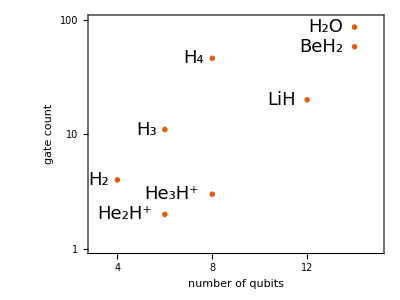

```mathematica
ListLogPlot[{gatesgrow},Joined->{False,True},
LabelStyle->{FontFamily->"FreeSerif",FontSize->18,Background->None},FrameLabel->{"number of qubits","gate count"},ImageSize->400,
Frame->True,FrameStyle->Directive[Black,24],PlotRange->{{3,15},{1,100}},PlotMarkers->"OpenMarkers",
AspectRatio->3/4,Background->White,PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Range[4,14,2],Automatic}},GridLines->Automatic]
```

```mathematica
Export["/home/cica/chemistry/img/vqe-best-gates.pdf",%]
```

/home/cica/chemistry/img/vqe-best-gates.pdf

```mathematica
runsum=<|#->summary[#,data]&/@Keys@hamiltonians|>;
```

Gate count: doubles, singles

```mathematica
Print@Grid[Table[{k,ToString@CountGates[bestressimp[k][[2]]]},{k,molecules}]]
```

H2 | {3, 1}
He2H | {1, 1}
He3H | {1, 2}
H3 | {8, 3}
LiH | {12, 8}
H4 | {36, 10}
H2O | {50, 36}
BeH2 | {39, 19}

Percentage of success

```mathematica
percentsucc=<|Table[k->ToString[IntegerPart[N[(succres[k]//Length),2]*10]]<>"%",{k,molecules}]|>
```

<|H2→100%,He2H→100%,He3H→100%,H3→100%,LiH→50%,H4→60%,H2O→30%,BeH2→80%|>

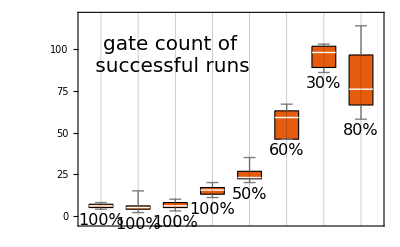

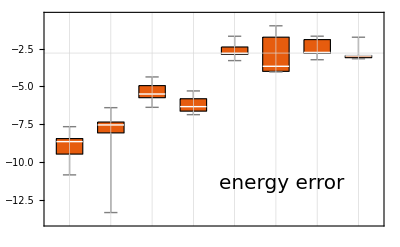

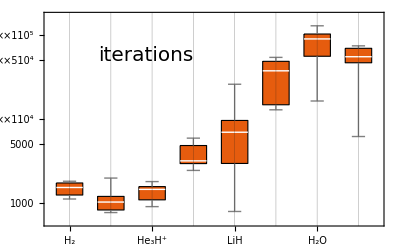

```mathematica
plotngates=BoxWhiskerChart[Values@Table[k->Select[runsum[k],#["ϵ"]<=chemacc&][[All,"ngates"]],{k,molecules}],FrameStyle->Directive[Black,20,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],GridLines->{Range[Length@molecules],None},PlotTheme->"Scientific",GridLinesStyle->GrayLevel[0.1,0.3],Epilog->Text[Style["gate count of\n successful runs",20,FontFamily->"FreeSerif",Background->White],Scaled[{.3,.8}]],ImageSize->400,
ImagePadding->{{60,10},{0,10}},ChartLabels->Placed[Table[percentsucc[m],{m,molecules}],Below],LabelStyle->Directive[Black,16, FontFamily->"FreeSerif"]
]

plotacc=BoxWhiskerChart[Values@Table[k->runsum[k][[All,"ϵ"]],{k,molecules}],ScalingFunctions->"Log10",FrameStyle->Directive[Black,20,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],GridLines->{Range[Length@molecules],{Log10@chemacc}},GridLinesStyle->{GrayLevel[0.1,0.3], Directive[Red,Thick ,Dashed]},PlotTheme->"Scientific",Epilog->Text[Style["energy error",20,FontFamily->"FreeSerif",Background->White],Scaled[{.7,.2}]],ImageSize->400,
ImagePadding->{{60,10},{0,0}}
]

plotfev=BoxWhiskerChart[Values@Table[k->runsum[k][[All,"nfev"]],{k,molecules}],ScalingFunctions->"Log10",FrameStyle->Directive[Black,20,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],ChartLabels->Placed[Table[labels[m],{m,molecules}],Axis,Rotate[#,30Degree]&],GridLines->{Range[Length@molecules],None},PlotTheme->"Scientific",GridLinesStyle->GrayLevel[0.1,0.3],Epilog->Text[Style["iterations",20,FontFamily->"FreeSerif",Background->White],Scaled[{.3,.8}]],ImageSize->400,
ImagePadding->{{60,10},{44,0}}
]
```

```mathematica
whiskers=Column[{plotngates,plotacc,plotfev},Spacings->-0.1];
```

```mathematica
Export["/home/cica/chemistry/img/whiskers.pdf",whiskers]
```

/home/cica/chemistry/img/whiskers.pdf

Best results

H2, ϵ=1.3614×10^-11

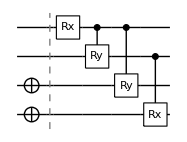

{Rx_3[-0.225571],C_3[Ry_2[-3.14159]],C_3[Ry_1[-3.14159]],C_2[Rx_0[3.14159]]}

He2H, ϵ=4.35207×10^-14

-Graphics-

{Rx_5[-0.143461],C_5[Rx_1[3.1416]]}

He3H, ϵ=0.000041779

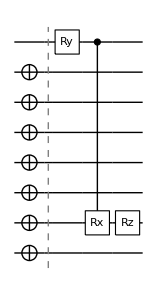

{Ry_7[-0.144889],C_7[Rx_1[3.14683]],Rz_1[1.57321]}

H3, ϵ=6.60757×10^-7

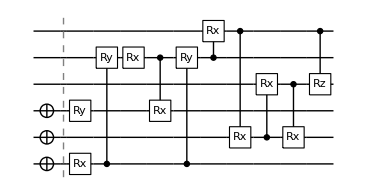

{Rx_0[0.639324],C_0[Ry_4[-0.450426]],Ry_2[-3.14159],Rx_4[-3.14274],C_4[Rx_2[3.14159]],C_0[Ry_4[3.14159]],C_4[Rx_5[-3.14159]],C_5[Rx_1[-3.14159]],C_1[Rx_3[-0.130514]],C_3[Rx_1[3.14159]],C_5[Rz_3[3.13751]]}

LiH, ϵ=0.00144262

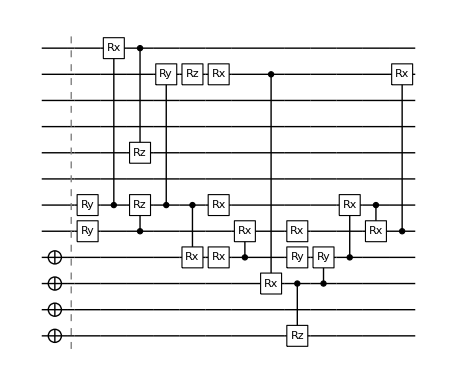

{Ry_4[-0.427556],Ry_5[0.259126],C_5[Rx_11[3.14159]],C_4[Rz_5[3.14228]],C_11[Rz_7[-2.20992]],C_5[Ry_10[3.01332]],C_5[Rx_3[0.0750935]],Rz_10[2.01433],Rx_5[3.14159],Rx_3[-0.0732942],Rx_10[-0.141451],C_3[Rx_4[-0.980303]],C_10[Rx_2[-3.1451]],Rx_4[1.40785],Ry_3[3.13702],C_2[Rz_0[3.09742]],C_2[Ry_3[-3.1356]],C_3[Rx_5[-3.14159]],C_5[Rx_4[-1.004]],C_4[Rx_10[3.14165]]}

H4, ϵ=0.000107323

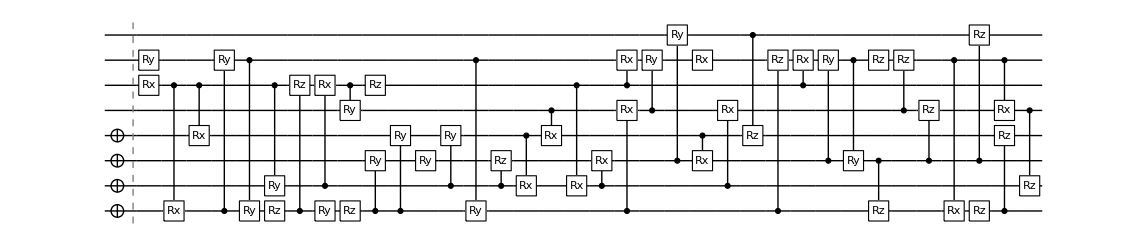

{Ry_6[-5.01215],Rx_5[-0.447751],C_5[Rx_0[-2.18482]],C_5[Rx_3[-3.14159]],C_0[Ry_6[-1.10473]],C_6[Ry_0[2.14363]],Rz_0[2.26137],C_5[Ry_1[3.14159]],C_0[Rz_5[-1.01277]],C_1[Rx_5[-0.745823]],Ry_0[-0.397902],C_5[Ry_4[3.14159]],Rz_0[-2.54331],C_0[Ry_2[-3.14159]],Rz_5[1.69031],C_0[Ry_3[-3.14159]],Ry_2[3.14159],C_1[Ry_3[3.14159]],C_6[Ry_0[0.48104]],C_1[Rz_2[2.48932]],C_3[Rx_1[0.42395]],C_4[Rx_3[3.14159]],C_5[Rx_1[-0.801594]],C_1[Rx_2[-3.14159]],C_0[Rx_4[3.14159]],C_5[Rx_6[2.19064]],C_4[Ry_6[3.06035]],C_2[Ry_7[-3.14159]],Rx_6[1.47973],C_3[Rx_2[3.14159]],C_1[Rx_4[-3.14159]],C_7[Rz_3[6.88408]],C_0[Rz_6[11.0253]],C_5[Rx_6[2.52634]],C_2[Ry_6[-1.5476]],C_6[Ry_2[-3.14159]],C_2[Rz_0[2.0566]],Rz_6[2.34183],C_4[Rz_6[-2.06533]],C_2[Rz_4[-0.637346]],C_6[Rx_0[3.14159]],Rz_0[4.52915],C_2[Rz_7[-0.807813]],C_6[Rx_4[3.14159]],C_0[Rz_3[0.678976]],C_4[Rz_1[8.60447]]}

H2O, ϵ=0.0015335

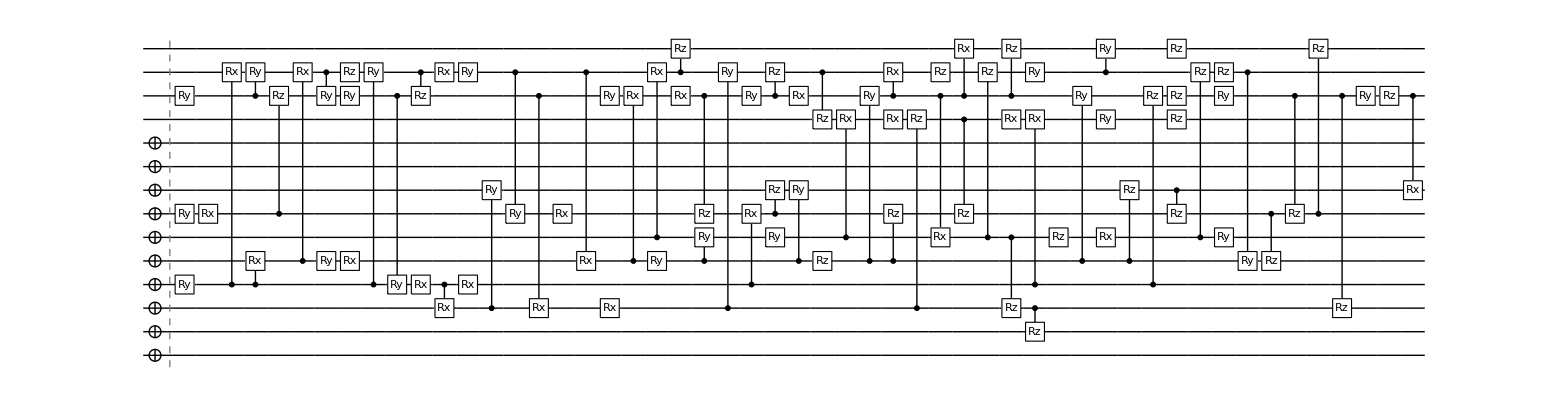

{Ry_11[4.71213],Ry_6[-0.129234],Ry_3[-0.0852519],Rx_6[-0.126058],C_3[Rx_12[2.7942]],C_11[Ry_12[-3.13136]],C_3[Rx_4[-0.34055]],C_6[Rz_11[1.61556]],C_4[Rx_12[-0.453808]],C_12[Ry_11[3.73587]],Ry_4[2.98811],Rx_4[2.89557],Ry_11[-3.85864],Rz_12[0.349583],C_3[Ry_12[1.17327]],C_11[Ry_3[3.07116]],C_12[Rz_11[1.75525]],Rx_3[-3.20192],Rx_12[1.02498],C_3[Rx_2[3.14159]],Ry_12[-0.829515],Rx_3[3.14159],C_12[Ry_6[6.5897]],C_2[Ry_7[3.14159]],Rx_6[0.0879427],C_12[Rx_4[3.45975]],C_11[Rx_2[-3.03737]],Ry_11[3.13743],C_4[Rx_11[0.824625]],Rx_2[-0.0660687],Ry_4[-0.16782],Rx_11[0.731695],C_11[Rz_6[-3.08227]],C_5[Rx_12[-1.35238]],C_3[Rx_6[0.0991102]],Ry_11[0.632415],C_12[Rz_13[6.38461]],C_4[Ry_5[-3.14159]],C_2[Ry_12[1.24057]],Ry_5[3.14159],C_6[Rz_7[2.35018]],C_4[Ry_7[3.14159]],C_11[Rz_12[-0.230347]],Rx_11[3.07281],C_12[Rz_10[3.70215]],Rz_4[-5.29874],C_5[Rx_10[-3.14161]],C_4[Ry_11[-0.955739]],Rx_10[-1.57079],C_11[Rx_12[-1.67649]],C_4[Rz_6[-1.13703]],C_2[Rz_10[3.14131]],C_11[Rx_5[3.14159]],Rz_12[0.260989],C_11[Rx_13[-3.14159]],C_5[Rz_12[-6.42]],C_10[Rz_6[3.1422]],C_5[Rz_2[-1.6681]],Rx_10[1.41523],C_11[Rz_13[4.83567]],C_2[Rz_1[-3.81819]],Rz_5[3.41273],C_3[Rx_10[-1.79186]],C_4[Ry_11[-3.1317]],Rx_5[1.5708],Ry_10[1.57078],C_4[Rz_7[3.03383]],C_3[Rz_11[1.75923]],Ry_12[1.4915],Rz_10[-4.62257],Rz_11[2.73855],C_7[Rz_6[-2.28632]],C_12[Ry_13[-3.14159]],Ry_11[1.57021],C_5[Rz_12[-3.1416]],Rz_13[-5.66309],Rz_12[-8.16561],Ry_5[-1.5708],C_12[Ry_4[-9.42478]],C_6[Rz_4[1.79488]],C_11[Rz_6[3.0914]],C_6[Rz_13[1.60066]],C_11[Rz_2[3.13839]],Ry_11[-1.56512],Rz_11[-0.270007],C_11[Rx_7[-3.14159]]}

BeH2, ϵ=0.00107872

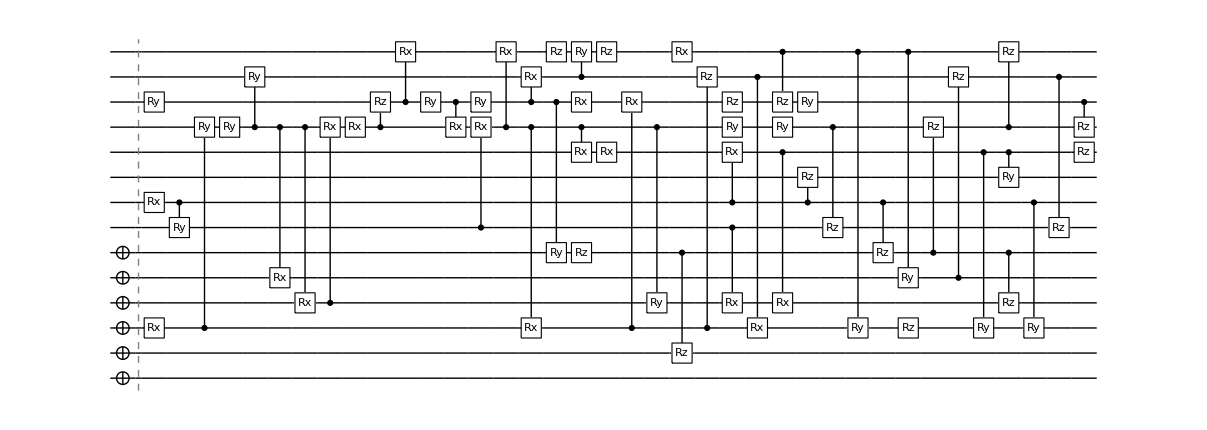

{Rx_7[0.103933],Ry_11[1.61049],Rx_2[0.21159],C_7[Ry_6[3.14159]],C_2[Ry_10[3.14159]],Ry_10[-3.14159],C_10[Ry_12[3.14159]],C_10[Rx_4[3.14159]],C_10[Rx_3[3.14159]],C_3[Rx_10[-5.17648]],Rx_10[5.15993],C_10[Rz_11[3.05497]],C_11[Rx_13[0.22893]],Ry_11[-4.61794],C_11[Rx_10[-0.146951]],Ry_11[3.03828],C_6[Rx_10[0.15291]],C_10[Rx_13[-7.47513]],C_11[Rx_12[-3.14159]],C_10[Rx_2[-3.14159]],C_11[Ry_5[-3.14159]],Rz_13[1.77639],C_10[Rx_9[-0.078271]],C_12[Ry_13[-1.06936]],Rx_11[1.5708],Rz_5[-1.80925],Rz_13[-1.77887],Rx_9[0.104306],C_2[Rx_11[-3.14159]],C_10[Ry_3[3.14159]],Rx_13[-0.117151],C_2[Rz_12[2.47824]],Rz_11[-1.5708],Ry_10[-2.32375],C_6[Rx_3[3.14159]],C_5[Rz_1[-3.14664]],C_7[Rx_9[-0.10424]],C_12[Rx_2[-3.14159]],Ry_10[2.32375],C_13[Rz_11[-3.14159]],C_9[Rx_3[3.14159]],C_7[Rz_8[2.51243]],Ry_11[-1.5708],C_10[Rz_6[1.85823]],C_13[Ry_2[-3.14159]],C_7[Rz_5[1.18618]],C_13[Ry_4[3.14159]],Rz_2[0.762759],C_5[Rz_10[-2.66896]],C_4[Rz_12[1.6493]],C_9[Ry_2[-3.14159]],C_5[Rz_3[-0.66406]],C_10[Rz_13[1.76347]],C_9[Ry_8[3.14159]],C_7[Ry_2[-3.14159]],C_12[Rz_6[1.9843]],C_11[Rz_10[0.368477]],Rz_9[-0.661187]}

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[
Print[mol,", ϵ=",bestressimp[mol][[1]]-groundstates[mol]];
Print@DrawCircuit[{initcirc[mol],bestressimp[mol][[2]]}];
Print[bestressimp[mol][[2]]];
,{mol,molecules}]
```

### Rounding the results: module ?roundingAnsatzIterate

```mathematica
succres=<| Table[mol->GetSuccData[mol] ,{mol,Keys@hamiltonians}]|>;
```

```mathematica
ClearAll[roundingAnsatzIterate]
roundingAnsatzIterate::usage="roundingAnsatzIterate[ansatz,θvars,ansatzinit,hamiltonian,ψ,ψwork,accuracy,maxfrac]. Iterate the rounding to π/j, where j is increased up to maxfrac. Iteration stops when energy difference is less than the accuracy.";
roundingAnsatzIterate[ansatz_,θvars_,ansatzinit_,hamiltonian_,ψ_,ψwork_,accuracy_,maxfrac_]:=Module[
{idx=0,newkeys,ansatznew,θvarsnew,frac,newcost,cost}
,
newkeys=Table[k->Subscript[θ, idx++],{k,Keys@θvars}];
ansatznew=ansatz/.newkeys;
frac=1;
While[frac<= maxfrac,
θvarsnew=<|Table[  (k/.newkeys)->Round[θvars[k] ,π/frac] ,{k,Keys@θvars}] |>;
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,ansatznew]/.θvarsnew];
newcost=CalcExpecPauliSum[ψ,hamiltonian,ψwork];
If[(newcost-cost)<=accuracy,Break[]];
frac++;
];
{ansatznew/.θvarsnew,newcost}
]
```

```mathematica
bestres=<|Table[
mol->succres[mol][[First@Ordering[Length[#[[1]]]&/@succres[mol],1]]],{mol,Keys@hamiltonians}]|>;
```

maxfrac=200;
accuracy=10^-4;
roundRes=Table[
molecule->
With[{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[X_i,{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
result=bestres[molecule]
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
{ansatz,newcost}=roundingAnsatzIterate[result[[1]],result[[2]],ansatzinit,hamiltonian,ψ,ψwork,accuracy,maxfrac];
Print["Best result of ",molecule," has ϵ=",newcost-groundstate];
{ansatz,newcost,newcost-groundstate,Length@ansatz}
],{molecule,Keys@hamiltonians}];

Best result of BeH2 has ϵ=0.00131873

Best result of LiH has ϵ=0.00151079

Best result of H2O has ϵ=0.00179457

Best result of H2 has ϵ=0.0000129511

Best result of H3 has ϵ=0.0000123006

Best result of H4 has ϵ=0.000192186

Best result of He2H has ϵ=1.23311×10^-6

Best result of He3H has ϵ=0.0000447107

roundRes = <|roundRes|>;

DumpSave["roundRes.mx", roundRes];

```mathematica
roundRes<<"roundRes.mx"
```

Null roundRes

------ Molecule BeH2 ϵ=0.00131873 ngates=58 ------

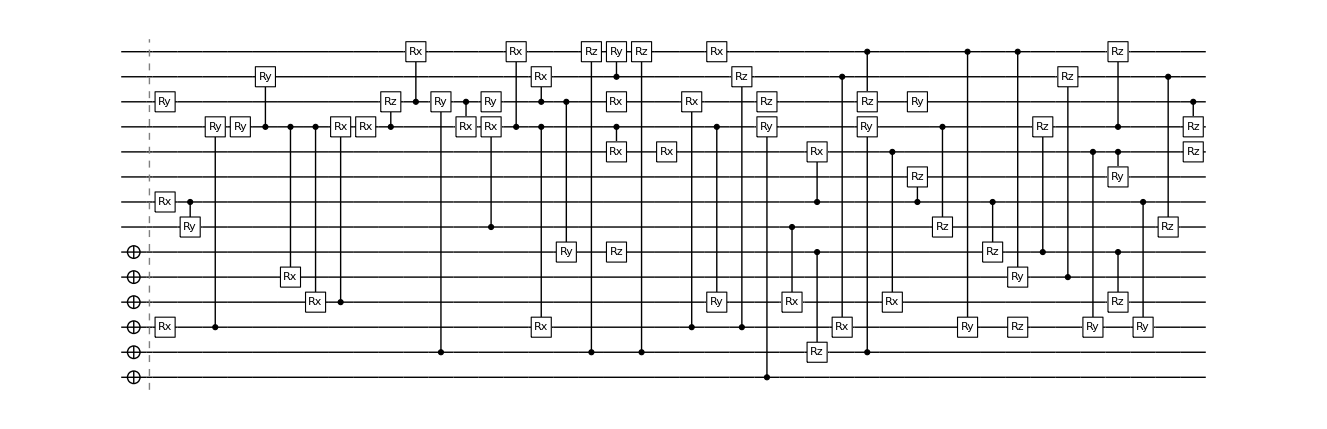

{Rx_7[(7 π)/200],Ry_11[(103 π)/200],Rx_2[(13 π)/200],C_7[Ry_6[π]],C_2[Ry_10[π]],Ry_10[-π],C_10[Ry_12[π]],C_10[Rx_4[π]],C_10[Rx_3[π]],C_3[Rx_10[-(33 π)/20]],Rx_10[(41 π)/25],C_10[Rz_11[(97 π)/100]],C_11[Rx_13[(3 π)/40]],C_1[Ry_11[-(147 π)/100]],C_11[Rx_10[-(9 π)/200]],Ry_11[(193 π)/200],C_6[Rx_10[π/20]],C_10[Rx_13[-(119 π)/50]],C_11[Rx_12[-π]],C_10[Rx_2[-π]],C_11[Ry_5[-π]],C_1[Rz_13[(113 π)/200]],C_10[Rx_9[-π/40]],C_12[Ry_13[-(17 π)/50]],Rx_11[π/2],Rz_5[-(23 π)/40],C_1[Rz_13[-(113 π)/200]],Rx_9[(7 π)/200],C_2[Rx_11[-π]],C_10[Ry_3[π]],Rx_13[-(7 π)/200],C_2[Rz_12[(79 π)/100]],Rz_11[-π/2],C_0[Ry_10[-(37 π)/50]],C_6[Rx_3[π]],C_5[Rz_1[-π]],C_7[Rx_9[-(7 π)/200]],C_12[Rx_2[-π]],C_1[Ry_10[(37 π)/50]],C_13[Rz_11[-π]],C_9[Rx_3[π]],C_7[Rz_8[(4 π)/5]],Ry_11[-π/2],C_10[Rz_6[(59 π)/100]],C_13[Ry_2[-π]],C_7[Rz_5[(19 π)/50]],C_13[Ry_4[π]],Rz_2[(49 π)/200],C_5[Rz_10[-(17 π)/20]],C_4[Rz_12[(21 π)/40]],C_9[Ry_2[-π]],C_5[Rz_3[-(21 π)/100]],C_10[Rz_13[(14 π)/25]],C_9[Ry_8[π]],C_7[Ry_2[-π]],C_12[Rz_6[(63 π)/100]],C_11[Rz_10[(23 π)/200]],Rz_9[-(21 π)/100]}

------ Molecule LiH ϵ=0.00151079 ngates=20 ------

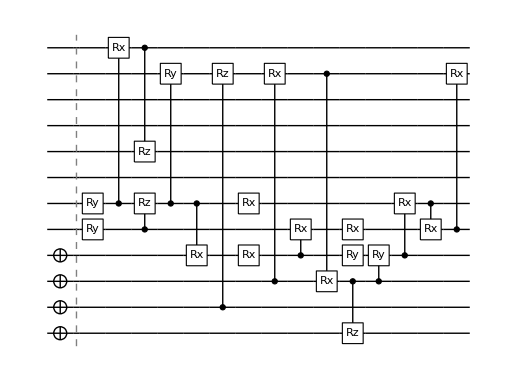

{Ry_4[-(27 π)/200],Ry_5[(2 π)/25],C_5[Rx_11[π]],C_4[Rz_5[π]],C_11[Rz_7[-(141 π)/200]],C_5[Ry_10[(24 π)/25]],C_5[Rx_3[π/40]],C_1[Rz_10[(16 π)/25]],Rx_5[π],Rx_3[-π/40],C_2[Rx_10[-(9 π)/200]],C_3[Rx_4[-(31 π)/100]],C_10[Rx_2[-π]],Rx_4[(9 π)/20],Ry_3[π],C_2[Rz_0[(197 π)/200]],C_2[Ry_3[-π]],C_3[Rx_5[-π]],C_5[Rx_4[-(8 π)/25]],C_4[Rx_10[π]]}

------ Molecule H2O ϵ=0.00179457 ngates=86 ------

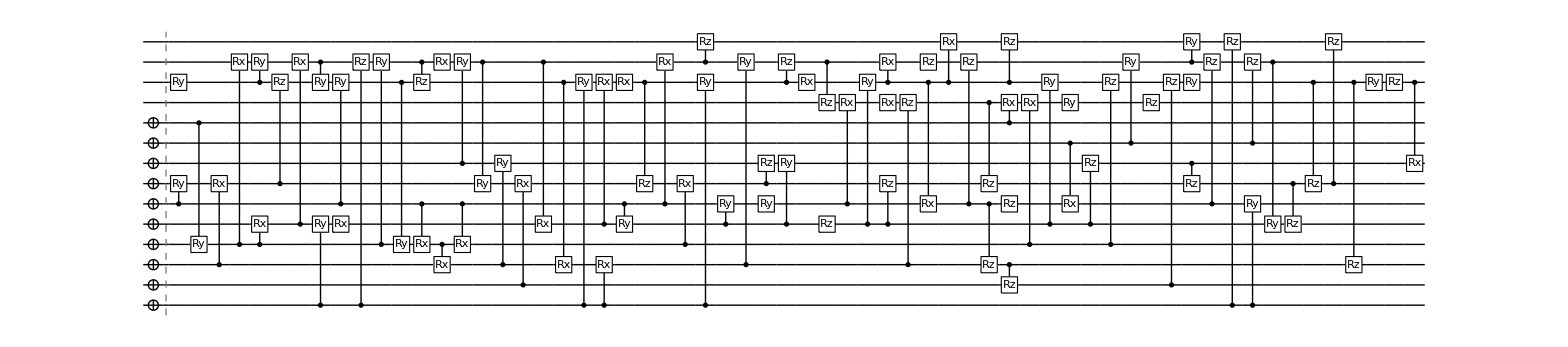

{Ry_11[(3 π)/2],C_5[Ry_6[-π/25]],C_9[Ry_3[-π/40]],C_2[Rx_6[-π/25]],C_3[Rx_12[(89 π)/100]],C_11[Ry_12[-(199 π)/200]],C_3[Rx_4[-(11 π)/100]],C_6[Rz_11[(103 π)/200]],C_4[Rx_12[-(29 π)/200]],C_12[Ry_11[(119 π)/100]],C_0[Ry_4[(19 π)/20]],Rx_4[(23 π)/25],C_5[Ry_11[-(123 π)/100]],C_0[Rz_12[(11 π)/100]],C_3[Ry_12[(3 π)/8]],C_11[Ry_3[(49 π)/50]],C_12[Rz_11[(14 π)/25]],C_5[Rx_3[-(51 π)/50]],Rx_12[(13 π)/40],C_3[Rx_2[π]],C_7[Ry_12[-(53 π)/200]],C_5[Rx_3[π]],C_12[Ry_6[(21 π)/10]],C_2[Ry_7[π]],C_1[Rx_6[(3 π)/100]],C_12[Rx_4[(11 π)/10]],C_11[Rx_2[-(193 π)/200]],C_0[Ry_11[π]],C_4[Rx_11[(13 π)/50]],C_0[Rx_2[-π/50]],C_5[Ry_4[-(11 π)/200]],Rx_11[(47 π)/200],C_11[Rz_6[-(49 π)/50]],C_5[Rx_12[-(43 π)/100]],C_3[Rx_6[(3 π)/100]],C_0[Ry_11[π/5]],C_12[Rz_13[(203 π)/100]],C_4[Ry_5[-π]],C_2[Ry_12[(79 π)/200]],Ry_5[π],C_6[Rz_7[(3 π)/4]],C_4[Ry_7[π]],C_11[Rz_12[-(3 π)/40]],Rx_11[(49 π)/50],C_12[Rz_10[(59 π)/50]],Rz_4[-(337 π)/200],C_5[Rx_10[-π]],C_4[Ry_11[-(61 π)/200]],Rx_10[-π/2],C_11[Rx_12[-(107 π)/200]],C_4[Rz_6[-(9 π)/25]],C_2[Rz_10[π]],C_11[Rx_5[π]],Rz_12[(17 π)/200],C_11[Rx_13[-π]],C_5[Rz_12[-(409 π)/200]],C_10[Rz_6[π]],C_5[Rz_2[-(53 π)/100]],C_9[Rx_10[(9 π)/20]],C_11[Rz_13[(77 π)/50]],C_2[Rz_1[-(243 π)/200]],Rz_5[(217 π)/200],C_3[Rx_10[-(57 π)/100]],C_4[Ry_11[-(199 π)/200]],C_8[Rx_5[π/2]],Ry_10[π/2],C_4[Rz_7[(193 π)/200]],C_3[Rz_11[(14 π)/25]],C_8[Ry_12[(19 π)/40]],Rz_10[-(147 π)/100],C_1[Rz_11[(87 π)/100]],C_7[Rz_6[-(73 π)/100]],C_12[Ry_13[-π]],Ry_11[π/2],C_5[Rz_12[-π]],C_0[Rz_13[-(361 π)/200]],C_8[Rz_12[-(13 π)/5]],C_0[Ry_5[-π/2]],C_12[Ry_4[-3 π]],C_6[Rz_4[(57 π)/100]],C_11[Rz_6[(197 π)/200]],C_6[Rz_13[(51 π)/100]],C_11[Rz_2[π]],Ry_11[-π/2],Rz_11[-(17 π)/200],C_11[Rx_7[-π]]}

------ Molecule H2 ϵ=0.0000129511 ngates=4 ------

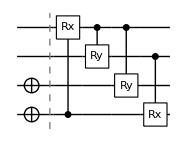

{C_0[Rx_3[-(7 π)/100]],C_3[Ry_2[-π]],C_3[Ry_1[-π]],C_2[Rx_0[π]]}

------ Molecule H3 ϵ=0.0000123006 ngates=11 ------

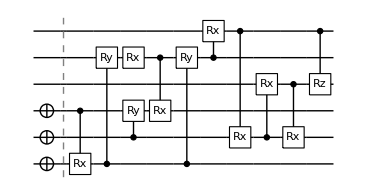

{C_2[Rx_0[(41 π)/200]],C_0[Ry_4[-(29 π)/200]],C_1[Ry_2[-π]],Rx_4[-π],C_4[Rx_2[π]],C_0[Ry_4[π]],C_4[Rx_5[-π]],C_5[Rx_1[-π]],C_1[Rx_3[-π/25]],C_3[Rx_1[π]],C_5[Rz_3[π]]}

------ Molecule H4 ϵ=0.000192186 ngates=46 ------

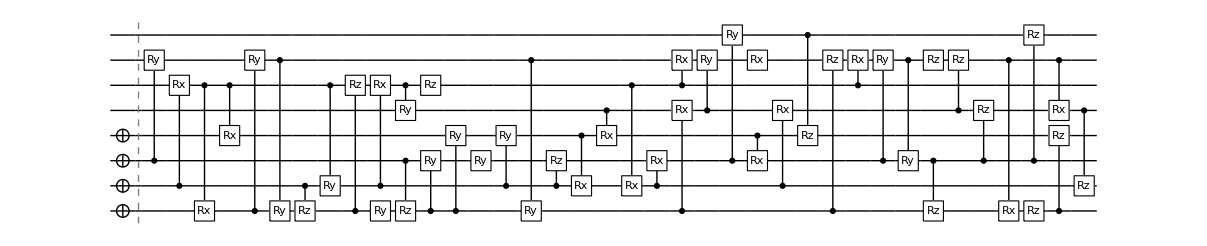

{C_2[Ry_6[-(319 π)/200]],C_1[Rx_5[-(29 π)/200]],C_5[Rx_0[-(139 π)/200]],C_5[Rx_3[-π]],C_0[Ry_6[-(7 π)/20]],C_6[Ry_0[(17 π)/25]],C_1[Rz_0[(18 π)/25]],C_5[Ry_1[π]],C_0[Rz_5[-(8 π)/25]],C_1[Rx_5[-(47 π)/200]],Ry_0[-π/8],C_5[Ry_4[π]],C_2[Rz_0[-(81 π)/100]],C_0[Ry_2[-π]],Rz_5[(27 π)/50],C_0[Ry_3[-π]],Ry_2[π],C_1[Ry_3[π]],C_6[Ry_0[(31 π)/200]],C_1[Rz_2[(79 π)/100]],C_3[Rx_1[(27 π)/200]],C_4[Rx_3[π]],C_5[Rx_1[-(51 π)/200]],C_1[Rx_2[-π]],C_0[Rx_4[π]],C_5[Rx_6[(139 π)/200]],C_4[Ry_6[(39 π)/40]],C_2[Ry_7[-π]],Rx_6[(47 π)/100],C_3[Rx_2[π]],C_1[Rx_4[-π]],C_7[Rz_3[(219 π)/100]],C_0[Rz_6[(351 π)/100]],C_5[Rx_6[(161 π)/200]],C_2[Ry_6[-(99 π)/200]],C_6[Ry_2[-π]],C_2[Rz_0[(131 π)/200]],Rz_6[(149 π)/200],C_4[Rz_6[-(131 π)/200]],C_2[Rz_4[-(41 π)/200]],C_6[Rx_0[π]],Rz_0[(36 π)/25],C_2[Rz_7[-(51 π)/200]],C_6[Rx_4[π]],C_0[Rz_3[(43 π)/200]],C_4[Rz_1[(137 π)/50]]}

------ Molecule He2H ϵ=1.23311×10^-6 ngates=2 ------

-Graphics-

{C_3[Rx_5[-(9 π)/200]],C_5[Rx_1[π]]}

------ Molecule He3H ϵ=0.0000447107 ngates=3 ------

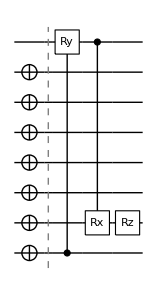

{C_0[Ry_7[-(9 π)/200]],C_7[Rx_1[π]],Rz_1[π/2]}

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[
Print["------ Molecule ",k," ϵ=",roundRes[k][[3]]," ngates=",Length@roundRes[k][[1]]," ------"];
Print[DrawCircuit[{Subscript[X, #]&/@Range[0,occupations[k]-1],roundRes[k][[1]]}]];
Print[roundRes[k][[1]]];
,{k,Keys@hamiltonians}]
```

### Rounding θ, if possible: module ?roundingAnsatzSoft

```mathematica
ClearAll[roundingAnsatzSoft]
roundingAsatzSoft::usage="roundingAnsatzSoft[ansatz,θvars,ansatzinit,hamiltonian,ψ,ψwork,fraction_of_π,decimal,θerr]. Rounding to multiplication of fraction if rounding difference is less than θerr, otherwise rounded to dec decimals.";
roundingAnsatzSoft[ansatz_,θvars_,ansatzinit_,hamiltonian_,ψ_,ψwork_,fraction_,decimal_,θerr_]:=Module[
{idx=0,newkeys,ansatznew,θvarsnew,newcost,cost,roundθ}
,
newkeys=Table[k->Subscript[θ, idx++],{k,Keys@θvars}];
ansatznew=ansatz/.newkeys;

θvarsnew=<|Table[  
roundθ=Round[θvars[k] ,π/fraction] ;
(k/.newkeys)->If[Abs[roundθ-θvars[k]]<=θerr,roundθ,Round[θvars[k],N[1.0*10^-decimal]]] 
,{k,Keys@θvars}] 
|>;
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,ansatznew]/.θvarsnew];
newcost=CalcExpecPauliSum[ψ,hamiltonian,ψwork];

{ansatznew/.θvarsnew,newcost}
]
```

accuracy=10^-2;
fraction=2;
decimal=2;
roundsoftRes=<|Table[
molecule->
With[{
nqubits=hamiltonians[[All,3]][molecule],
hamiltonian=hamiltonians[[All,1]][molecule],
ansatzinit=Table[X_i,{i,Range[0,occupations[molecule]-1]}],
groundstate=groundstates[molecule],
result=bestres[molecule]
},
{ψ,ψwork}=CreateQuregs[nqubits,2];
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,result[[1]]]/.result[[2]]];
oldcost=CalcExpecPauliSum[ψ,hamiltonian,ψwork];

{ansatz,newcost}=roundingAnsatzSoft[result[[1]],result[[2]],ansatzinit,hamiltonian,ψ,ψwork,fraction,decimal,accuracy];
Print@Column@{"Best result of "<>molecule<>" has ϵ_new="<>ToString[newcost-groundstate,FortranForm]<>", ϵ_before="<>ToString[oldcost-groundstate,FortranForm],DrawCircuit[ansatz,nqubits],ansatz};
{ansatz,newcost,newcost-groundstate,Length@ansatz}
],{molecule,Keys@hamiltonians}]|>;

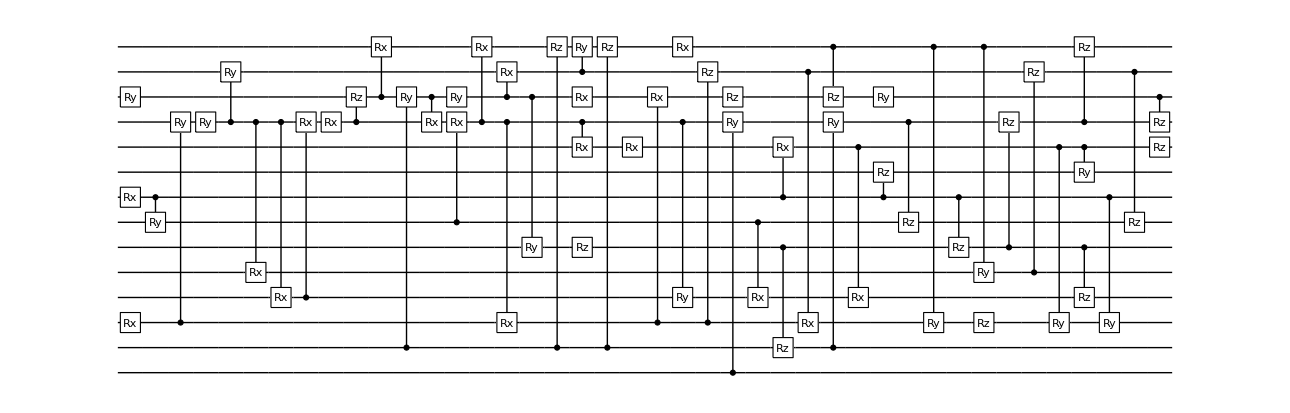
Best result of BeH2 has ϵ_new=0.0010995874444343912, ϵ_before=0.0010787209879996595
-Graphics-
{Rx_7[0.1],Ry_11[1.61],Rx_2[0.21],C_7[Ry_6[π]],C_2[Ry_10[π]],Ry_10[-π],C_10[Ry_12[π]],C_10[Rx_4[π]],C_10[Rx_3[π]],C_3[Rx_10[-5.18]],Rx_10[5.16],C_10[Rz_11[3.05]],C_11[Rx_13[0.23]],C_1[Ry_11[-4.62]],C_11[Rx_10[-0.15]],Ry_11[3.04],C_6[Rx_10[0.15]],C_10[Rx_13[-7.48]],C_11[Rx_12[-π]],C_10[Rx_2[-π]],C_11[Ry_5[-π]],C_1[Rz_13[1.78]],C_10[Rx_9[-0.08]],C_12[Ry_13[-1.07]],Rx_11[π/2],Rz_5[-1.81],C_1[Rz_13[-1.78]],Rx_9[0.1],C_2[Rx_11[-π]],C_10[Ry_3[π]],Rx_13[-0.12],C_2[Rz_12[2.48]],Rz_11[-π/2],C_0[Ry_10[-2.32]],C_6[Rx_3[π]],C_5[Rz_1[-π]],C_7[Rx_9[-0.1]],C_12[Rx_2[-π]],C_1[Ry_10[2.32]],C_13[Rz_11[-π]],C_9[Rx_3[π]],C_7[Rz_8[2.51]],Ry_11[-π/2],C_10[Rz_6[1.86]],C_13[Ry_2[-π]],C_7[Rz_5[1.19]],C_13[Ry_4[π]],Rz_2[0.76],C_5[Rz_10[-2.67]],C_4[Rz_12[1.65]],C_9[Ry_2[-π]],C_5[Rz_3[-0.66]],C_10[Rz_13[1.76]],C_9[Ry_8[π]],C_7[Ry_2[-π]],C_12[Rz_6[1.98]],C_11[Rz_10[0.37]],Rz_9[-0.66]}

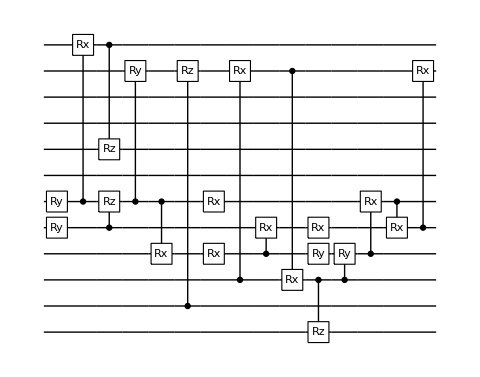
Best result of LiH has ϵ_new=0.0014445519822849917, ϵ_before=0.0014426249126735513
-Graphics-
{Ry_4[-0.43],Ry_5[0.26],C_5[Rx_11[π]],C_4[Rz_5[π]],C_11[Rz_7[-2.21]],C_5[Ry_10[3.01]],C_5[Rx_3[0.08]],C_1[Rz_10[2.01]],Rx_5[π],Rx_3[-0.07],C_2[Rx_10[-0.14]],C_3[Rx_4[-0.98]],C_10[Rx_2[-π]],Rx_4[1.41],Ry_3[π],C_2[Rz_0[3.1]],C_2[Ry_3[-π]],C_3[Rx_5[-π]],C_5[Rx_4[-1.]],C_4[Rx_10[π]]}

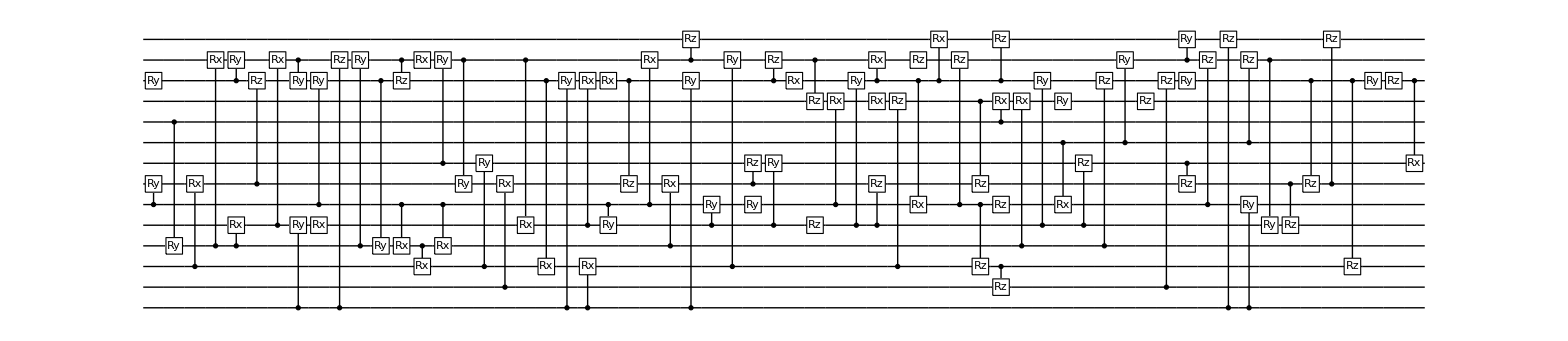
Best result of H2O has ϵ_new=0.0016979349874475247, ϵ_before=0.0015334962047148792
-Graphics-
{Ry_11[(3 π)/2],C_5[Ry_6[-0.13]],C_9[Ry_3[-0.09]],C_2[Rx_6[-0.13]],C_3[Rx_12[2.79]],C_11[Ry_12[-3.13]],C_3[Rx_4[-0.34]],C_6[Rz_11[1.62]],C_4[Rx_12[-0.45]],C_12[Ry_11[3.74]],C_0[Ry_4[2.99]],Rx_4[2.9],C_5[Ry_11[-3.86]],C_0[Rz_12[0.35]],C_3[Ry_12[1.17]],C_11[Ry_3[3.07]],C_12[Rz_11[1.76]],C_5[Rx_3[-3.2]],Rx_12[1.02],C_3[Rx_2[π]],C_7[Ry_12[-0.83]],C_5[Rx_3[π]],C_12[Ry_6[6.59]],C_2[Ry_7[π]],C_1[Rx_6[0.09]],C_12[Rx_4[3.46]],C_11[Rx_2[-3.04]],C_0[Ry_11[π]],C_4[Rx_11[0.82]],C_0[Rx_2[-0.07]],C_5[Ry_4[-0.17]],Rx_11[0.73],C_11[Rz_6[-3.08]],C_5[Rx_12[-1.35]],C_3[Rx_6[0.1]],C_0[Ry_11[0.63]],C_12[Rz_13[6.38]],C_4[Ry_5[-π]],C_2[Ry_12[1.24]],Ry_5[π],C_6[Rz_7[2.35]],C_4[Ry_7[π]],C_11[Rz_12[-0.23]],Rx_11[3.07],C_12[Rz_10[3.7]],Rz_4[-5.3],C_5[Rx_10[-π]],C_4[Ry_11[-0.96]],Rx_10[-π/2],C_11[Rx_12[-1.68]],C_4[Rz_6[-1.14]],C_2[Rz_10[π]],C_11[Rx_5[π]],Rz_12[0.26],C_11[Rx_13[-π]],C_5[Rz_12[-6.42]],C_10[Rz_6[π]],C_5[Rz_2[-1.67]],C_9[Rx_10[1.42]],C_11[Rz_13[4.84]],C_2[Rz_1[-3.82]],Rz_5[3.41],C_3[Rx_10[-1.79]],C_4[Ry_11[-π]],C_8[Rx_5[π/2]],Ry_10[π/2],C_4[Rz_7[3.03]],C_3[Rz_11[1.76]],C_8[Ry_12[1.49]],Rz_10[-4.62],C_1[Rz_11[2.74]],C_7[Rz_6[-2.29]],C_12[Ry_13[-π]],Ry_11[π/2],C_5[Rz_12[-π]],C_0[Rz_13[-5.66]],C_8[Rz_12[-8.17]],C_0[Ry_5[-π/2]],C_12[Ry_4[-3 π]],C_6[Rz_4[1.79]],C_11[Rz_6[3.09]],C_6[Rz_13[1.6]],C_11[Rz_2[π]],Ry_11[-π/2],Rz_11[-0.27],C_11[Rx_7[-π]]}

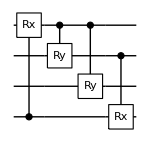
Best result of H2 has ϵ_new=7.965721122271674e-6, ϵ_before=1.361399881716352e-11
-Graphics-
{C_0[Rx_3[-0.23]],C_3[Ry_2[-π]],C_3[Ry_1[-π]],C_2[Rx_0[π]]}

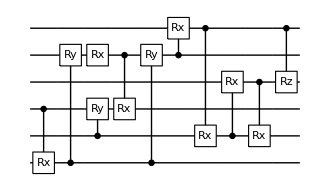
Best result of H3 has ϵ_new=8.441777374912363e-7, ϵ_before=6.60757461190542e-7
-Graphics-
{C_2[Rx_0[0.64]],C_0[Ry_4[-0.45]],C_1[Ry_2[-π]],Rx_4[-π],C_4[Rx_2[π]],C_0[Ry_4[π]],C_4[Rx_5[-π]],C_5[Rx_1[-π]],C_1[Rx_3[-0.13]],C_3[Rx_1[π]],C_5[Rz_3[π]]}

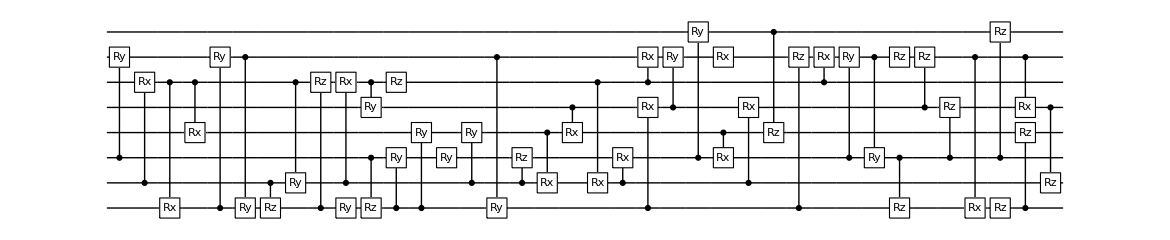
Best result of H4 has ϵ_new=0.0001367896658350798, ϵ_before=0.00010732297367055388
-Graphics-
{C_2[Ry_6[-5.01]],C_1[Rx_5[-0.45]],C_5[Rx_0[-2.18]],C_5[Rx_3[-π]],C_0[Ry_6[-1.1]],C_6[Ry_0[2.14]],C_1[Rz_0[2.26]],C_5[Ry_1[π]],C_0[Rz_5[-1.01]],C_1[Rx_5[-0.75]],Ry_0[-0.4],C_5[Ry_4[π]],C_2[Rz_0[-2.54]],C_0[Ry_2[-π]],Rz_5[1.69],C_0[Ry_3[-π]],Ry_2[π],C_1[Ry_3[π]],C_6[Ry_0[0.48]],C_1[Rz_2[2.49]],C_3[Rx_1[0.42]],C_4[Rx_3[π]],C_5[Rx_1[-0.8]],C_1[Rx_2[-π]],C_0[Rx_4[π]],C_5[Rx_6[2.19]],C_4[Ry_6[3.06]],C_2[Ry_7[-π]],Rx_6[1.48],C_3[Rx_2[π]],C_1[Rx_4[-π]],C_7[Rz_3[6.88]],C_0[Rz_6[11.03]],C_5[Rx_6[2.53]],C_2[Ry_6[-1.55]],C_6[Ry_2[-π]],C_2[Rz_0[2.06]],Rz_6[2.34],C_4[Rz_6[-2.07]],C_2[Rz_4[-0.64]],C_6[Rx_0[π]],Rz_0[4.53],C_2[Rz_7[-0.81]],C_6[Rx_4[π]],C_0[Rz_3[0.68]],C_4[Rz_1[8.6]]}

Best result of He2H has ϵ_new=3.383765386999471e-6, ϵ_before=4.3520742565306136e-14
-Graphics-
{C_3[Rx_5[-0.14]],C_5[Rx_1[π]]}

Best result of He3H has ϵ_new=0.000047777493634271195, ϵ_before=0.00004177900040502891
-Graphics-
{C_0[Ry_7[-0.14]],C_7[Rx_1[π]],Rz_1[π/2]}

### Print some ansatze to quantikz format

DumpSave["roundsoftRes.mx", roundsoftRes];

```mathematica
roundsoftRes<<"roundsoftRes.mx"
```

Null roundsoftRes

```mathematica
roundsoftRes["LiH"]
```

roundsoftRes[LiH]

```mathematica
inits=Join[ConstantArray[1,4],ConstantArray[0,8]]
```

{1,1,1,1,0,0,0,0,0,0,0,0}

```mathematica
Directory[]
```

/home/cica/postox/papers/chemistry-code/vqe/results

```mathematica
circ2quantikz[inits,roundsoftRes["LiH"][[1]],"lih.tex"]
```

circ2quantikz[{1,1,1,1,0,0,0,0,0,0,0,0},LiH,lih.tex]

## Other people results

https://journals.aps.org/prxquantum/abstract/10.1103/PRXQuantum.2.020337
feature: fixed ansatz with permutation accounted which improves the accuracy

```mathematica
ansatz1[nq_,singles_,nlayer_]:=Table[
If[OddQ@layer,
Flatten@{Table[Subscript[s, q],{s,singles},{q,Range[0,nq-1]}],Table[Subscript[C, q-1][Subscript[X, q]],{q,Range[1,nq-1,2]}]}
,
Flatten@{Table[Subscript[s, q],{s,singles},{q,Range[1,nq-2]}],
Table[Subscript[C, i-1][Subscript[X, i]],{i,2,nq-2,2}]}
],{layer,nlayer}]
```

LiH

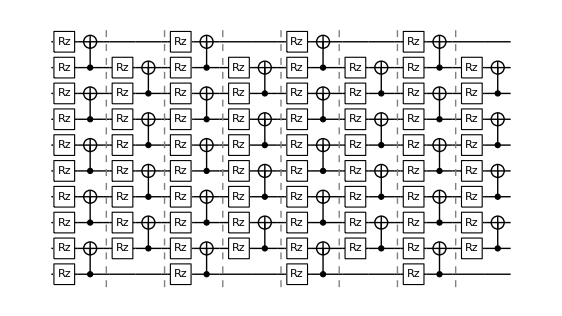

108

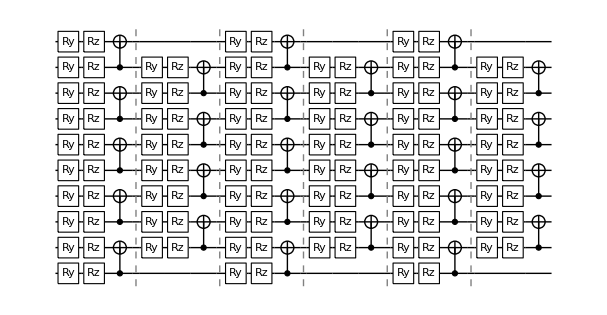

135

```mathematica
nq=10;
ansatz=ansatz1[nq,{Rz},8];
DrawCircuit[ansatz,nq]
Length@Flatten@ansatz

ansatz=ansatz1[nq,{Ry,Rz},6];
DrawCircuit[ansatz,nq]
Length@Flatten@ansatz
```

```mathematica
CountGates[Flatten@ansatz1[nq,{Rz},10]]
```

{45,90}

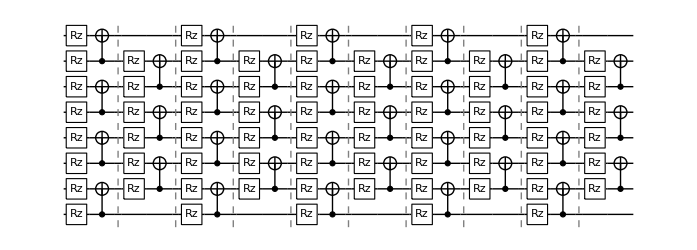

105

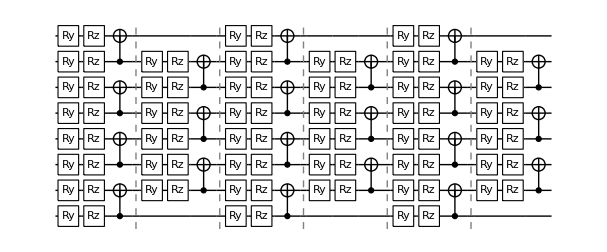

105

```mathematica
nq=8;
ansatz=ansatz1[nq,{Rz},10];
DrawCircuit[ansatz,nq]
Length@Flatten@ansatz

ansatz=ansatz1[nq,{Ry,Rz},6];
DrawCircuit[ansatz,nq]
Length@Flatten@ansatz
```

## Analysis on the hardness of the ground state: entanglement

Reference : https://arxiv.org/pdf/2111.03132.pdf,https://arxiv.org/pdf/2107.09155.pdf

```mathematica
VonNeumann[σ_]:=-Total[#*Log2[#]&/@σ]
```

```mathematica
GSInfo::usage="GSInfo[hamiltonian], return the analysis of the ground state of a hamiltonian."
GSInfo[hamiltonian_]:=Module[{eigvecs,eigs,gsidx,C,dim,u,σ,v,scoeff,vnentropy},
{eigs,eigvecs}=Eigensystem[CalcPauliSumMatrix[hamiltonian]];
gsidx=Ordering[eigs,1]//First;

(*reshape into bipartite state, then perfom SVD*)
dim=Sqrt@Length@eigvecs[[gsidx]];
C=ArrayReshape[eigvecs[[gsidx]],{dim,dim}];
{u,σ,v}=SingularValueDecomposition[C];
(*schmidt form*)
scoeff=Select[Diagonal@σ,#>0&];
vnentropy=VonNeumann[scoeff];
<|"eigvec"->eigvecs[[gsidx]], "eigval"->eigs[[gsidx]],"svd"->{u,σ,v},"srank"->Length@scoeff,"vnentropy"->vnentropy |>
]
```

GSInfo[hamiltonian], return the analysis of the ground state of a hamiltonian.

gsinfo = <|Table[
    Print["gather info on molecule ", mol];
    mol -> GSInfo[hamiltonians[mol][[1]]], {mol, hamiltonians // Keys}]
   |>;

gather info on molecule BeH2

gather info on molecule LiH

gather info on molecule H2O

gather info on molecule H2

gather info on molecule H3

gather info on molecule H4

gather info on molecule He2H

gather info on molecule He3H

```mathematica
gsinfo<<gsinfo.mx;
```

```mathematica
Table[gsinfo[m]["vnentropy"]=VonNeumann[Select[Diagonal@gsinfo[m]["svd"][[2]],#>0&]],{m,molecules}]
```

{0.363812,0.276227,0.27742,1.28719,0.947925,3.07336,1.97236,2.00669}

```mathematica
labelpos=<|"BeH2"->Left,"LiH"->Right,"H2O"->Right,"H2"->None,"H3"->Right,"H4"->Right,"He2H"->None,"He3H"->Above|>
```

<|BeH2→Left,LiH→Right,H2O→Right,H2→None,H3→Right,H4→Right,He2H→None,He3H→Above|>

```mathematica
srank=Table[Labeled[{N@Log2[gsinfo[mol]["srank"]],Around@(Length@#&/@succres[mol][[All,1]])},labels[mol],labelpos[mol],Background->None,FrameMargins->0],{mol,molecules}]/.{"He_3H^+":>"He_3H^+\nHe_2H^+\nH_2"}
```

{Labeled[{1.,6.01.5},H_2,None,Background→None,FrameMargins→0],Labeled[{1.,6.4.},He_2H^+,None,Background→None,FrameMargins→0],Labeled[{1.,6.62.3},He_3H^+
He_2H^+
H_2,Above,Background→None,FrameMargins→0],{3.,15.42.9}H_3,{3.,25.6.}LiH,{4.,57.9.}H_4,{4.64386,96.9.}H_2O,{5.67243,81.20.}BeH_2}

```mathematica
vnentropy=Table[Labeled[{gsinfo[mol]["vnentropy"],bestres
[mol][[1]]//Length},labels[mol]],{mol,molecules}]
```

{{0.363812,4}H_2,{0.276227,2}He_2H^+,{0.27742,3}He_3H^+,{1.28719,11}H_3,{0.947925,20}LiH,{3.07336,46}H_4,{1.97236,86}H_2O,{2.00669,58}BeH_2}

```mathematica
groundstates
```

<|H2O→-75.014,LiH→-7.88206,H2→-1.13728,H4→-1.99615,He2H→-5.76993,He3H→-8.57531,BeH2→-15.5952,H3→-1.41989|>

```mathematica
sranktwo=Table[Labeled[{N@Log2[gsinfo[mol]["srank"]],Around@(CountGates[#][[1]]&/@
sucressimp[mol][[All,2]])},labels[mol],labelpos[mol],Background->None,FrameMargins->0],{mol,molecules}]/.{"He_3H^+":>"H_2\nHe_2H^+\nHe_3H^+"}
```

{Labeled[{1.,3.91.2},H_2,None,Background→None,FrameMargins→0],Labeled[{1.,1.60.7},He_2H^+,None,Background→None,FrameMargins→0],Labeled[{1.,2.61.0},H_2
He_2H^+
He_3H^+,Above,Background→None,FrameMargins→0],{3.,10.51.8}H_3,{3.,16.4.}LiH,{4.,43.7.}H_4,{4.64386,62.12.}H_2O,{5.67243,51.12.}BeH_2}

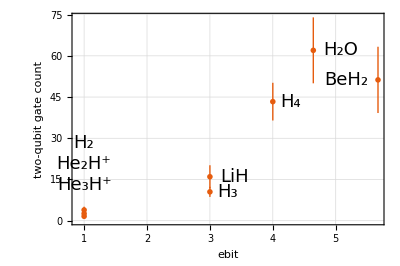

```mathematica
ListPlot[sranktwo,
LabelStyle->{FontFamily->"FreeSerif",FontSize->18,Background->None},FrameLabel->{"ebit","two-qubit gate count"},ImageSize->400,
Frame->True,FrameStyle->Directive[Black,20],PlotRange->All,PlotMarkers->"OpenMarkers",
AspectRatio->2/3,Background->White,PlotTheme->"Scientific",GridLines->Automatic]
```

```mathematica
Export["/home/cica/chemistry/img/sranktwo.pdf",%]
```

/home/cica/chemistry/img/sranktwo.pdf

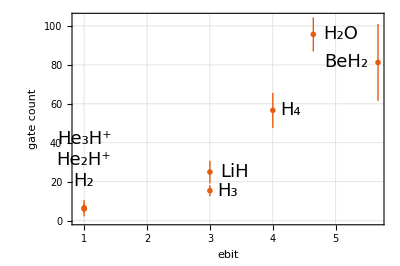

```mathematica
ListPlot[srank,
LabelStyle->{FontFamily->"FreeSerif",FontSize->18,Background->None},FrameLabel->{"ebit","gate count"},ImageSize->400,
Frame->True,FrameStyle->Directive[Black,20],PlotRange->All,PlotMarkers->"OpenMarkers",
AspectRatio->2/3,Background->White,PlotTheme->"Scientific",GridLines->Automatic]
```

```mathematica
Export["/home/cica/chemistry/img/srank.pdf",%]
```

/home/cica/chemistry/img/srank.pdf

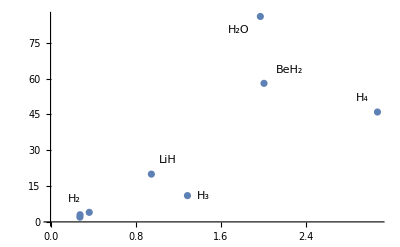

```mathematica
ListPlot[vnentropy]
```

```mathematica
bestressimp["He2H"][[-1]]
DrawCircuit[%,6]
```

{Rx_5[-0.143461],C_5[Rx_1[3.1416]]}

-Graphics-

```mathematica
hamiltonians["He2H"][[-1]]
occupations["He2H"]
```

6

5

```mathematica
gs=gsinfo["He2H"]["eigvec"]//Chop
-1+Ordering[gs,-2]
BaseForm[#,2]&/@(-1+Ordering[gs,-2])
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.997428,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.071669,0,0}

{61,31}

{111101_2,11111_2}

```mathematica
gsinfo["He3H"]["eigvec"]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.997377,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.005658,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0721544,0}